```mathematica
Needs["Notation`"];
```

```mathematica
Needs["MaTeX`"];
```

```mathematica
(*$RecursionLimit=100*)
```

```mathematica
(*p1 = {p10,p11,p12,p13};
p2 = {p20,p21,p22,p23};
q = {q0,q1,q2,q3};
l = {l0, l1,l2, l3};
b = {b0, b1,b2,b3};
Q = {Q0,Q1,Q2,Q3};*)
```

```mathematica
(*eta = DiagonalMatrix[{1,-1,-1,-1}];*)
```

```mathematica
(*ClearAll[p1,p2,q,l,b, Q, eta];
vecRules = {p1 -> {p10,p11,p12,p13},
p2 -> {p20,p21,p22,p23},
q -> {q0,q1,q2,q3},
l -> {l0, l1,l2, l3},
b -> {b0, b1,b2,b3},
(*Q -> {Q0,Q1,Q2,Q3},*)
Qp -> {Qp0, Qp1, Qp2, Qp3},
eta -> DiagonalMatrix[{1,-1,-1,-1}]};*)
```

```mathematica
(*RealQ[num_] := TrueQ[Refine[Element[num, Reals]]];
IsReal[x_] := FreeQ[RealQ[x],x∈Reals];*)
```

```mathematica
(*scalars = {x1, x2, m1, m2, S};
IsScalar[x_]:=MemberQ[scalars, x]||NumberQ[x]*)
```

```mathematica
ClearAll[scalars];
scalars={x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ};

$Assumptions=And@@(Element[#,Reals]&/@scalars);

IsScalar[expr_]:=Module[{vars, dotExp},
vars = Variables[expr];
dotExp = Cases[vars,holdDot[_,_]];
vars=Complement[vars,dotExp];
vars =Join[vars,HoldForm/@dotExp];

(vars==={}&&NumericQ[expr])||(vars=!={}&&SubsetQ[scalars,vars])
];

(*IsScalar[expr_]:=Module[{vars},
vars=Variables[expr];

(vars==={}&&NumericQ[expr])||(vars=!={}&&SubsetQ[scalars,vars])
];*)
```

```mathematica
scalars
```

{x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ}

```mathematica
AddToScalars[expr_]:=(If[!MemberQ[scalars,HoldForm[expr]],scalars=Append[scalars,HoldForm[expr]]];
expr);

AddDotProdToScalars[vectors_]:=Module[{vecPairs},
(*vecPairs = Subsets[vectors,{2}];*)
vecPairs=DeleteDuplicatesBy[Tuples[vectors,2], Sort];
dotProdPairs = holdDot@@#&/@ vecPairs;
Do[AddToScalars[dotProd], {dotProd, dotProdPairs}];
];
```

```mathematica
holdDotDef:=(
ClearAll[holdDot];(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],a.eta.b,b.eta.a]];*)
(*holdDot/:holdDot[a_,b_]:=If[OrderedQ[{a,b}],holdDot[a,b],holdDot[b,a]];*)
(*holdDot/:holdDot[a_,b_]:=0/;(PossibleZeroQ[a]||PossibleZeroQ[b]);
holdDot/:holdDot[a_,b_]:=holdDot@@Sort[{a,b}]/;!OrderedQ[{a,b}];*)
holdDot[a_,b_]:=0/;(PossibleZeroQ[a]||PossibleZeroQ[b]);
holdDot[a_,b_]:=holdDot@@Sort[{a,b}]/;!OrderedQ[{a,b}];
holdDot[a_+b_, x_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, a_+b_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_,c_?IsScalar y_]:= c holdDot[x,y];
holdDot[c_?IsScalar x_, y_]:= c holdDot[x,y];
holdDot[x_, Times[holdDot[a_,b_], y_]]:= holdDot[a,b]×holdDot[x,y];
holdDot[Times[holdDot[a_,b_]x_], y_]:= holdDot[a,b]× holdDot[x,y];
(*holdDot[c_ x_,y_]:=c holdDot[x,y]/;FreeQ[c,_List];
holdDot[x_,c_ y_]:=c holdDot[x,y]/;FreeQ[c,_List];*)


Notation[ParsedBoxWrapper[RowBox[{"a_","⊙","b_"}]]⇔ParsedBoxWrapper[RowBox[{"holdDot","[","a_",",","b_","]"}]]];
)
```

```mathematica
holdDotDer:=(
(*ClearAll[holdDot];*)

SetOptions[D,NonConstants->{holdDot, Wedge}];
(*D[expr_holdDot,vars__]^:=Module[{x,y,z},*)
holdDot/:D[holdDot[a_,b_],vars__]:=Module[{x=a,y=b,z},
(*{x,y}=List@@expr;*)
z={vars}[[1]];
Which[
IsScalar[z]&&x===q&&y===q,
holdDot[D[Q,{vars}[[1]]],y]+holdDot[x,D[Q,{vars}[[1]]]],
IsScalar[z]&&x===q,
holdDot[D[Q,{vars}[[1]]],y],
IsScalar[z]&&y===q,
holdDot[x,D[Q,{vars}[[1]]]],
!IsScalar[{vars}[[1]]],
x×D[y,{vars}[[1]]]+y×D[x,{vars}[[1]]],
True,0]];
)
```

```mathematica
holdDotDef
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
vectors={p1,p2,q,l,l1,l2, Qp}
```

{p1,p2,q,l,l1,l2,Qp}

```mathematica
AddDotProdToScalars[vectors]
```

```mathematica
scalars
```

{x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ,p1⊙p1,p1⊙p2,p1⊙q,l⊙p1,l1⊙p1,l2⊙p1,p1⊙Qp,p2⊙p2,p2⊙q,l⊙p2,l1⊙p2,l2⊙p2,p2⊙Qp,q⊙q,l⊙q,l1⊙q,l2⊙q,q⊙Qp,l⊙l,l⊙l1,l⊙l2,l⊙Qp,l1⊙l1,l1⊙l2,l1⊙Qp,l2⊙l2,l2⊙Qp,Qp⊙Qp}

```mathematica
ClearAll[Wedge];

Wedge[x_,y_]:=0/;(x===y||PossibleZeroQ[x]||PossibleZeroQ[y]);
Wedge[a_+b_, x_]:=Wedge[a,x]+Wedge[b,x];
Wedge[x_, a_+b_]:=Wedge[x,a]+Wedge[x,b];
Wedge[x_,c_?IsScalar y_]:= c Wedge[x,y];
Wedge[c_?IsScalar x_, y_]:= c Wedge[x,y];
Wedge[x_,y_]:=-Wedge[y,x]/;OrderedQ[{y,x}];
Wedge[x_, Times[holdDot[a_,b_], y_]]:= holdDot[a,b]×Wedge[x,y];
Wedge[Times[holdDot[a_,b_]x_], y_]:= holdDot[a,b]× Wedge[x,y];
```

```mathematica
wedgeDer:=(SetOptions[D,NonConstants->{holdDot, Wedge}];
(*D[expr_Wedge,vars__]^:=Module[{x,y,z},*)
Wedge/:D[Wedge[a_,b_],vars__]:=Module[{x=a,y=b,z},
(*{x,y}=List@@expr;*)
z={vars}[[1]];
Which[
IsScalar[z]&&x===q&&y===q,
Wedge[D[Q,{vars}[[1]]],y]+Wedge[x,D[Q,{vars}[[1]]]],
IsScalar[z]&&x===q,
Wedge[D[Q,{vars}[[1]]],y],
IsScalar[z]&&y===q,
Wedge[x,D[Q,{vars}[[1]]]],
!IsScalar[{vars}[[1]]],
Wedge[x,D[y,{vars}[[1]]]]+Wedge[D[x,{vars}[[1]]],y],
True,0]];

)
```

```mathematica
aWedgeDb[expr_, a_,b_]:= Wedge[a,D[expr,b]];
aWedgeDb[expr_holdDot, a_,b_]:= Module[{x,y}, {x,y}=List@@expr;
Wedge[a,y D[x,b]]+Wedge[a,x D[y,b]]];
```

```mathematica
(*ClearAll[holdDot]*)
(*SetAttributes[holdDot,HoldAll]*)
```

```mathematica
(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],HoldForm[a.eta.b],HoldForm[b.eta.a]]];*)
(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],a.eta.b,b.eta.a]];
holdDot[a_+b_, x_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, a_+b_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, c_?NumberQ y_]:= c holdDot[x,y];
holdDot[c_?NumberQ x_, y_]:= c holdDot[x,y];
holdDot[c_ x_,y_]:=c holdDot[x,y]/;FreeQ[c,_List];
holdDot[x_,c_ y_]:=c holdDot[x,y]/;FreeQ[c,_List];*)
```

```mathematica
(*UpValues[holdDot]={};
holdDot,Dt[holdDot[x_,y_], z,___]:=Which[
x===q&&y===q,
 holdDot[D[Q, z],y]+holdDot[x,D[Q, z]],
x===q,
holdDot[D[Q,z],y],
y===q,
holdDot[x,D[Q, z]],
True,
 0 ]*)

(*holdDot/:D[holdDot[x_,y_],z_,NonConstants->_]:=D[holdDot[x,y],z]*)
```

```mathematica
(*wrapDot[expr_ ] :=expr //.{(p1.eta.p1/.vecRules)->Subscript[m, 1]^2,(-p1.eta.p1/.vecRules)->-Subscript[m, 1]^2,(p2.eta.p2/.vecRules)->Subscript[m, 2]^2,(-p2.eta.p2/.vecRules)->-Subscript[m, 2]^2,
(p1.eta.p2/.vecRules)->γ,(-p1.eta.p2/.vecRules)->-γ,(p1.eta.q/.vecRules)->p1.eta.q,(-p1.eta.q/.vecRules)->-p1.eta.q,(p2.eta.q/.vecRules)->p2.eta.q,(-p2.eta.q/.vecRules)->-p2.eta.q,(p1.eta.l/.vecRules)->p1.eta.l,(-p1.eta.l/.vecRules)->-p1.eta.l,(p2.eta.l/.vecRules)->p2.eta.l,(-p2.eta.l/.vecRules)->-p2.eta.l,(l.eta.q/.vecRules)->l.eta.q,(-l.eta.q/.vecRules)->-l.eta.q,
(l.eta.l/.vecRules)->l.eta.l,(-l.eta.l/.vecRules)->-l.eta.l,
(q.eta.q/.vecRules)->q.eta.q,(-q.eta.q/.vecRules)->-q.eta.q}*)
```

```mathematica
(*holdDot[a_, b_]:=a.eta.b//FullSimplify//.{p1.eta.p2->HoldForm[HoldPattern[γ],-p1.eta.p2->-HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],-p1.eta.q->-HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],-p2.eta.q->-HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],-p1.eta.l->-HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],-p2.eta.l->-HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q],-l.eta.q->-HoldForm[l.eta.q]}*)
```

```mathematica
(*wrapDot[expr_, ] :=expr //.{p1.eta.p2->HoldForm[γ],-p1.eta.p2->-HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],-p1.eta.q->-HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],-p2.eta.q->-HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],-p1.eta.l->-HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],-p2.eta.l->-HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q],-l.eta.q->-HoldForm[l.eta.q],
l.eta.l->HoldForm[l.eta.l],-l.eta.l->-HoldForm[l.eta.l],
q.eta.q->HoldForm[q.eta.q],-q.eta.q->-HoldForm[q.eta.q]}*)
```

```mathematica
(*holdDot[expr_] :=Simplify[expr ,{p1.eta.p2->HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q]}]*)
```

```mathematica
holdDotDef
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
α1= (γ x2-m2^2 x1)/S;
α2 = (γ x1-m1^2 x2)/S;
Q = α1 p1+α2 p2+Qp;
q == Q;
```

```mathematica
holdDotDer
```

```mathematica
wedgeDer
```

```mathematica
D[holdDot[p1,q]/holdDot[p2,q],x1]
```

-(p1⊙q (-(m2^2 p1⊙p2)/S+(γ p2⊙p2)/S))/(p2⊙q)^2+(-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S)/(p2⊙q)

```mathematica
onShellP[expr_]:=expr//.{p1⊙q->0, p2⊙q->0,p1⊙p2->γ, p1⊙p1->m1^2,p2⊙p2->m2^2}
(*onShellP[expr_]:=expr//.{HoldForm[p1.eta.q]->0, HoldForm[p2.eta.q]->0}*)
```

```mathematica
(*simplifiedForm[expr_]:=expr/.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1}/.{(coef1_ ϵ+coef2_ l⊙p1)^(n_)->(coef2)^n*(ϵ*(coef1/coef2)/Abs[coef1/coef2]+l⊙p1)^n,(coef1_ ϵ+coef2_ l⊙p2)^(n_)->(coef2)^n*(ϵ*(coef1/coef2)/Abs[coef1/coef2]+l⊙p2)^n}*)
```

```mathematica
(-(m1^2 m2^2)/(W*S)+γ^2/(W*S))/.(T1:-m1^2 m2^2/c_.)+(T2:γ^2/c_.):>S/c
```

-(m1^2 m2^2)/(S W)+γ^2/(S W)

```mathematica
simplifiedForm[expr_]:=expr/.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1,-m1^2 m2^2+γ^2->S,m1^2 m2^2-γ^2->-S}//.{(coef1_. ϵ+coef2_. l1dot_+rest_.)^(n_.):>(coef2)^n*(ϵ*(coef1/coef2)/Abs[coef1/coef2]+l1dot+Distribute[rest/coef2])^n/;l1dot==l⊙p1||l1dot==l⊙p2||l1dot==l1⊙p1||l1dot==l1⊙p2||l1dot==l2⊙p1||l1dot==l2⊙p2}
```

```mathematica
cancelFactors[expr_]:=expr//.{ dot1:d1_^(n_.)*(c1_. ϵ+ dot2:d2_+d3___)^(m_)/;d1==d2+d3->If[Abs[n]<Abs[m],(c1 ϵ+ d1)^(m+n),d1^(m+n)]}
```

```mathematica
factorRho[exp_]:=exp/.{(expr_Plus)^(n_):>Factor[expr]^n/;ContainsAll[Variables[expr], {ϵ,l⊙p1}]||ContainsAll[Variables[expr], {ϵ,l⊙p2}]}
```

```mathematica
simplifyTerm[expr_]:=expr//.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
simplifyTerm[expr_]:=expr//.{(num_ Power[a_,m_:1])/(Power[den_,-n_:1]):>num Power[a,m-1]/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
simplifyTerm[expr_]:=(lst={};
Do[AppendTo[lst,expr[[i]]//.{(num_ Power[a_,m_:1])/(Power[den_,-n_:1]):>num Power[a,m-1]/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}],{i,1,Length[expr]}];
Total[lst]);
```

```mathematica
cancelFactors[expr_]:=expr//.{ dot1:d1_^(n_.)*(c1_. ϵ+ dot2:d2_+d3___)^(m_)/;d1==d2+d3->If[Abs[n]<Abs[m],(c1 ϵ+ d1)^(m+n),d1^(m+n)]}
```

```mathematica
wedgeToDot[expr_]:=expr/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}
```

```mathematica
extractLog[expr_,expnt_]:=Coefficient[factorRho[simplifyTerm[Expand[simplifiedForm[onShellP[expr]]]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,expnt]
```

```mathematica
delx:=(D[#,{x1,1}]-D[#,{x2,1}])&;
```

```mathematica
L[1] = 1/((p1⊙l+ⅈ ϵ)(p2⊙l-ⅈ ϵ));
L[2] = 1/((p1⊙l+ⅈ ϵ)(p2⊙(q-l)-ⅈ ϵ));
L[3] = 1/((p1⊙(q-l)+ⅈ ϵ)(p2⊙(q-l)-ⅈ ϵ));
L[4] = 1/((p1⊙(q-l)+ⅈ ϵ)(p2⊙l-ⅈ ϵ));
```

```mathematica
Cf[1] = (1/2)(2γ+ℏ (p2-p1)⊙l-(ℏ*γ l⊙l)/(p1⊙l+ⅈ ϵ)+(ℏ*γ l⊙l)/(p2⊙l-ⅈ ϵ));
Cf[2] = (1/2)(2γ+ℏ(p2+p1)⊙l-2ℏ*p1⊙q-(ℏ*γ l⊙l)/(p1⊙l+ⅈ ϵ)+(ℏ*γ(q-l)⊙(q-l))/(p2⊙(q-l)-ⅈ ϵ));
Cf[3] = (1/2)(2γ+ℏ(p2-p1)⊙(2q-l)-(ℏ*γ(q-l)⊙(q-l))/(p1⊙(q-l)+ⅈ ϵ)+(ℏ*γ(q-l)⊙(q-l))/(p2⊙(q-l)-ⅈ ϵ));
Cf[4] = (1/2)(2γ-ℏ(p2+p1)⊙l+2ℏ*p2⊙q-(ℏ*γ(q-l)⊙(q-l))/(p1⊙(q-l)+ⅈ ϵ)+(ℏ*γ l⊙l)/(p2⊙l-ⅈ ϵ));
```

```mathematica
A0[1] = ⅈ((2p1+ℏ(q+ρ*l))⊙(2p2-ℏ(q+ρ*l)))/((q-ρ*l)⊙(q-ρ*l));
A0[2] = ⅈ((2p1+ℏ(q+ρ*l))⊙(2p2-ℏ(q-ρ*l)))/((q-ρ*l)⊙(q-ρ*l));
A0[3] = ⅈ((2p1+ℏ(q-ρ*l))⊙(2p2-ℏ(q-ρ*l)))/((q-ρ*l)⊙(q-ρ*l));
A0[4] = ⅈ((2p1+ℏ(q-ρ*l))⊙(2p2-ℏ(q+ρ*l)))/((q-ρ*l)⊙(q-ρ*l));
```

```mathematica
Do[Do[Cfhbar[i][n] = Coefficient[Normal[Series[Cf[i], {ℏ, 0, n}]], ℏ, n];,{i,1,4}], {n, 0, 2}];
```

```mathematica
Do[Do[A0hbar[i][n] =Coefficient[Normal[Series[A0[i], {ℏ,0,n}]],ℏ,n];,{i,1,4}], {n,0,1}];
```

```mathematica
Do[Do[ Do[A0hbarl[i][n,m]= Coefficient[Normal[Series[A0hbar[i][n],{ρ,0,m}]], ρ, m],{i,1,4}];, {m,0,3 }], {n,0,1}];
```

```mathematica
D[p1⊙q,x1]
```

-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S

```mathematica
a1=aWedgeDb[A0[1]/.{ρ->0}, l1,p2]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c};

a2=aWedgeDb[aWedgeDb[A0[1]/.{ρ->0}, l1,p1]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c},p1,p1];

a3=aWedgeDb[aWedgeDb[A0[1]/.{ρ->0}, l1,p2]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c},p1,p1];

b1=D[Wedge[p1,q]*(aWedgeDb[A0[1]/.{ρ->0}, l1,p1]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}),x1];

b2=D[Wedge[p1,q]*(aWedgeDb[A0[1]/.{ρ->0}, l1,p2]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}),x1];

a1=simplifiedForm@onShellP@a1;
a2=simplifiedForm@onShellP@a2;
a3=simplifiedForm@onShellP@a3;
b1=simplifiedForm@onShellP@b1;
b2=simplifiedForm@onShellP@b2;
```

```mathematica
sum=0;
Do[sum+=L[i]*Cf[i],{i,{1,2,3,4}}];
```

```mathematica
ClearAll[a1,a2,a3,a4,a5,a6]
```

```mathematica
a1=Coefficient[extractLog[sum*(aWedgeDb[A0[1]/.{ρ->0},p1,p1]-D[Wedge[p1,q]*(A0[1]/.{ρ->0}),x1]),-2],ℏ,1]
```

(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
a2=Coefficient[extractLog[(aWedgeDb[sum/.{γ->p1⊙p2},p1,p1]-Wedge[p1,q]*D[sum,x1])*(A0[1]/.{ρ->0}),-2],ℏ,1]
```

(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)-(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
a3=Coefficient[extractLog[-(aWedgeDb[sum/.{γ->p1⊙p2},p1,p1]-Wedge[p1,q]*D[sum,x1])*(wedgeToDot[aWedgeDb[A0[1]/.ρ->0,l1,q]]),-2],ℏ,1]
```

-(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
a4=Coefficient[extractLog[-sum*(aWedgeDb[wedgeToDot[aWedgeDb[A0[1]/.ρ->0,l1,p1]],p1,p1]-D[Wedge[p1,q]*wedgeToDot[aWedgeDb[A0[1]/.ρ->0,l1,p1]],x1]),-2],ℏ,1]
```

-(2 ⅈ γ^2 p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(2 ⅈ γ^2 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
a2+a3+a4
```

-(2 ⅈ γ^2 p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(2 ⅈ γ^2 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
sum=0;
Do[sum+=L[i]*Cf[i],{i,{1,2,3,4}}];
```

```mathematica
b1=extractLog[D[sum*q⊙q*aWedgeDb[A0[1]/.ρ->0,p1,p1],x1]-D[sum*q⊙q*aWedgeDb[A0[1]/.ρ->0,p1,p1],x2],-2];
```

```mathematica
b2=extractLog[D[(A0[1]/.ρ->0)*q⊙q*aWedgeDb[sum,p1,p1],x1]-D[(A0[1]/.ρ->0)*q⊙q*aWedgeDb[sum,p1,p1],x2],-2];
```

```mathematica
b3=-extractLog[D[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]]*q⊙q*aWedgeDb[sum,p1,p1],x1]-D[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]]*q⊙q*aWedgeDb[sum,p1,p1],x2],-2];
```

```mathematica
b4=-extractLog[D[sum*q⊙q*aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],p1,p1],x1]-D[sum*q⊙q*aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],p1,p1],x2],-2];
```

```mathematica
b5=1/2 extractLog[D[wedgeToDot[aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],l1,q]]*q⊙q*aWedgeDb[sum,p1,p1],x1]-D[wedgeToDot[aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],l1,q]]*q⊙q*aWedgeDb[sum,p1,p1],x2],-2];
```

```mathematica
c1=extractLog[D[D[sum*Wedge[p1,q]*(A0[1]/.ρ->0),x1]-D[sum*Wedge[p1,q]*(A0[1]/.ρ->0),x2],x1],-2];
```

```mathematica
c2=-extractLog[D[D[sum*Wedge[p1,q]*q⊙q*wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],x1]-D[sum*Wedge[p1,q]*q⊙q*wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],x2],x1],-2];
```

```mathematica
c3=1/2 extractLog[D[D[sum*Wedge[p1,q]*q⊙q*wedgeToDot[aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],l1,q]],x1]-D[sum*Wedge[p1,q]*q⊙q*wedgeToDot[aWedgeDb[wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]],l1,q]],x2],x1],-2];
```

```mathematica
Coefficient[Expand[b1+b2+b3+b4+b5],ℏ,0]
```

```mathematica
Coefficient[Expand[c1+c2+c3],ℏ,0]-Coefficient[Expand[b1+b2+b3+b4+b5],ℏ,0]
```

```mathematica
wedgeToDot[aWedgeDb[(A0[1]/.ρ->0),l1,q]]
```

(ⅈ (-2 ℏ l⊙p1+2 ℏ l⊙p2-2 ℏ^2 l⊙q))/(q⊙q)-(2 ⅈ l⊙q (4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(q⊙q)^2

```mathematica
Coefficient[Expand[b3],ℏ,0]
```

-(16 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 ⅈ γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ m1^2 γ^2 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ m1^2 γ^2 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
extractLog[simplifyTerm[simplifiedForm[onShellP[Expand[sum]]]],-2]
```

-γ/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-γ/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
extractLog[Total[Select[List@@simplifyTerm[simplifiedForm[Expand[onShellP[aWedgeDb[sum,p1,p1]]]]],ContainsAll[List@@Numerator[#],{p1⋀q}&]]]-simplifyTerm[Expand[simplifiedForm[onShellP[p1⋀q D[sum,x1]]]]],-2]
```

(γ ℏ l⊙l p1⋀q)/(2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+(γ ℏ l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(ℏ p1⋀q)/(2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ ℏ l⊙l p1⋀q)/(2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(ℏ p1⋀q)/(2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(ℏ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ^2 ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
ClearAll[sum];
sum=0;
Do[sum+=L[i]*Cf[i]/.{γ->p1⊙p2},{i,{1,2,3,4}}];
```

```mathematica
extractLog[delx[(aWedgeDb[sum/.{γ->p1⊙p2},p1,p1]-Wedge[p1,q]*D[sum,x1])],-3]
```

-(2 γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(2 γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(6 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^4 (-ⅈ ϵ+l⊙p2))-(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^3)+(2 γ ℏ l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^3)+(4 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2)^2)-(6 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^4 (ⅈ ϵ+l⊙p2))-(p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)+(2 ℏ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)+(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(m2^2 γ ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ^2 ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
extractLog[simplifiedForm[onShellP[delx[sum]]],-5]
```

0

```mathematica
simplifyTerm[Expand[extractLog[simplifiedForm[onShellP[aWedgeDb[sum,p1,p1]-Wedge[p1,q]*D[sum,x1]]],-2]]]
```

-(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(p1⋀p2)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2)+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))

```mathematica
b1=simplifyTerm[Expand[extractLog[simplifiedForm[onShellP[aWedgeDb[sum12,p1,p1]-Wedge[p1,q]*D[sum12,x1]]],-3]]]
```

(γ ℏ q⊙q l⋀p1)/(2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(ℏ q⊙q p1⋀p2)/(2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)

```mathematica
b2=simplifyTerm[Expand[extractLog[simplifiedForm[onShellP[aWedgeDb[sum14,p1,p1]-Wedge[p1,q]*D[sum14,x1]]],-3]]]
```

-(γ ℏ q⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(ℏ q⊙q p1⋀p2)/(2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))

```mathematica
ClearAll[b3];
b3=extractLog[simplifiedForm[onShellP[sum]],-3]
```

-(γ ℏ q⊙q)/(2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ ℏ q⊙q)/(2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ ℏ q⊙q)/(2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ ℏ q⊙q)/(2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
Coefficient[simplifyTerm[Expand[onShellP[(aWedgeDb[wedgeToDot[aWedgeDb[A0[1]/.{ρ->0},l1,q]],p1,p1]-D[p1⋀q*wedgeToDot[aWedgeDb[A0[1]/.{ρ->0},l1,q]],x1])*b3]]],ℏ,1]
```

(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
b3=Total[Select[List@@b3,ContainsAll[List@@Numerator[#], {l⋀p1}]&]]
```

-(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))

```mathematica
Do[If[ContainsAll[List@@Numerator[b3[[i]]],{l⊙q,l⋀p1}],b3[[i]]=K4[b3[[i]]]],{i,1,Length[b3]}]
```

```mathematica
simplifyTerm[Expand[b3/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])}]]
```

(γ^2 p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^2 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^2 p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ^2 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(2 m1^2 γ ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^3)+(γ^2 ℏ l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(2 γ^2 ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(m1^2 γ ℏ l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(2 γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2)+(m1^2 γ ℏ p1⋀q)/(2 S (ⅈ ϵ+l⊙p1)^2)-(m1^2 γ ℏ l⊙p2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^3)-(γ ℏ l⊙l p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(2 S (ⅈ ϵ+l⊙p2)^2)+(γ ℏ l⊙l p1⋀q)/(2 S (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ^2 ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
extractLog[simplifyTerm[Expand[simplifiedForm[onShellP[sum]]]],-2]
```

-γ/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-γ/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
simplifiedForm[onShellP[sum12]]
```

(2 γ-(γ ℏ l⊙l)/(ⅈ ϵ+l⊙p1)+(γ ℏ l⊙l)/(-ⅈ ϵ+l⊙p2)+ℏ (-l⊙p1+l⊙p2))/(2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(2 γ-(γ ℏ l⊙l)/(ⅈ ϵ+l⊙p1)+ℏ (l⊙p1+l⊙p2)-(γ ℏ (l⊙l-2 l⊙q+q⊙q))/(ⅈ ϵ+l⊙p2))/(2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
a=extractLog[simplifiedForm[onShellP[aWedgeDb[sum,p1,p1]-Wedge[p1,q]*D[sum,x1]]],-2]/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])};
```

```mathematica
simplifyTerm[Expand[Total[Select[List@@a,ContainsAll[List@@Numerator[#],{p1⋀p2,l⊙q}](*&&ContainsNone[List@@Numerator[#],{l⊙q}]*)(*&&ContainsAll[List@@Denominator[#],{S^2}]*)&]]/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])}]]
```

(ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(2 γ^2 ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ^2 ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(ℏ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ^2 ℏ l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(m1^2 γ ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(2 γ^2 ℏ l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(m1^2 γ ℏ l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
K4[expr_]:=simplifyTerm[Expand[1/(2S)(expr/.{l⊙q l⋀p1->-p1⋀q})(m2^2 l⊙p1 l⊙p1+m1^2 l⊙p2 l⊙p2+l⊙l-2γ l⊙p1 l⊙p2)]];
```

```mathematica
K4[(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))]
```

(2 γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2)-(m1^2 γ ℏ l⊙p2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^3)-(γ ℏ l⊙l p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))

```mathematica
b=extractLog[simplifiedForm[onShellP[wsp]],-2];
```

```mathematica
extractLog[simplifiedForm[onShellP[delx[sum]]],-2]
```

-(γ ℏ l⊙l)/(2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙l)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(3 ℏ)/(2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(m2^2 γ ℏ)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^2 ℏ)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ ℏ l⊙l)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)-(γ ℏ l⊙l)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)-(γ ℏ l⊙l)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙l)/(2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(γ ℏ l⊙l)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-ℏ/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(m1^2 γ ℏ)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(2 γ^2 ℏ)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(3 ℏ)/(2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(m1^2 γ ℏ)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(γ^2 ℏ)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
sum=0;
Do[sum+=L[i]*Cf[i]/.{γ->p1⊙p2},{i,{1,2}}];

Expand[simplifiedForm@Coefficient[factorRho[simplifyTerm@Expand[onShellP[aWedgeDb[simplifiedForm@sum,l1,q]/.{Wedge[l1,c_]->(γ p2-m2^2 p1)⊙c/S,Wedge[c_,l1]->-(γ p2-m2^2 p1)⊙c/S}]/.{l->ρ l,ϵ->ρ ϵ}]],ρ,-3]]
```

$Aborted

```mathematica
aWedgeDb[Expand[L[i]*Cf[i]*(A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{i->1}]
,p1,p1]
```

```mathematica
ClearAll[sum10,sum11,sum20,sum21,sum]
```

```mathematica
sum10=0;
Do[term10=L[i]*Cf[i]*(A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{γ->p1⊙p2};

sum10+=simplifyTerm[Expand[Coefficient[factorRho[simplifiedForm[onShellP[aWedgeDb[term10,p1,p1]]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]]],{i,1,4}];
```

```mathematica
sum11=0;
Do[term11=q⊙q*L[i]*Cf[i]*(A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{γ->p1⊙p2};

sum11+=simplifyTerm@Expand[Coefficient[factorRho[simplifiedForm@onShellP[D[aWedgeDb[term11,p1,p1],x1]-D[aWedgeDb[term11,p1,p1],x2]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]],{i,1,4}];
```

```mathematica
sum20=0;
Do[term20=Wedge[p1,q]*L[i]*Cf[i]*(A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{γ->p1⊙p2};

sum20+=simplifyTerm[Expand[Coefficient[factorRho[simplifiedForm@onShellP[D[term20,x1]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]]],{i,1,4}];
```

```mathematica
sum21=0;
Do[term21=q⊙q*Wedge[p1,q]*L[i]*Cf[i]*(A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{γ->p1⊙p2};

sum21+=simplifyTerm@Expand[Coefficient[factorRho[simplifiedForm@onShellP[D[D[term21,x1],x1]-D[D[term21,x2],x1]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]],{i,1,4}];
```

```mathematica
simplifyTerm@Expand[((sum10-sum20)/ℏ-(sum11-sum21)/2/.{(l⊙q)^2->l⊙l*q⊙q}/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])})/.{l⊙q->0}]/.{Power[ℏ,-1]->0,Power[ℏ,1]->0}
```

```mathematica
Coefficient[simplifyTerm[Expand[sum10/ℏ]],ℏ,0]
```

-(2 ⅈ γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2 q⊙q)+(6 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(6 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
Coefficient[simplifyTerm@Expand[(sum11-sum21)],ℏ,0]
```

-(16 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 ⅈ γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)-(16 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(16 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(8 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(8 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
b=simplifyTerm@Expand[((sum10-sum20)/ℏ/.{(l⊙q)^2->l⊙l*q⊙q}/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])})/.{l⊙q->0}]
```

```mathematica
a1=ⅈ γ Wedge[p1,l]δ[p2⊙l](A0[1]/.{ρ->0})(1/(p1⊙l-ⅈ ϵ)^2-1/(p1⊙l+ⅈ ϵ)^2);
a2=ℏ γ l⊙q Wedge[p1,l](A0[1]/.{ρ->0})((-2ⅈ δ[p2⊙l])/(p1⊙l-ⅈ ϵ)^3-1/((p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2)+1/((p1⊙l+ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2));
a3=-ℏ γ q⊙q Wedge[p1,l](ⅈ δ[p2⊙l]/(p1⊙l-ⅈ ϵ)^3+1/(2(p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2)-1/(2(p1⊙l+ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2))onShellP[aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}];
a4=-(ℏ γ l⊙q Wedge[p1,q](1/((p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2)+(2ⅈ δ[p2⊙l])/(p1⊙l-ⅈ ϵ)^3)-ⅈ γ Wedge[p1,q] δ[p2⊙l]/(p1⊙l-ⅈ ϵ)^2)onShellP[aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}];
a5=((-ⅈ γ δ[p2⊙l])/(p1⊙l-ⅈ ϵ)^2+ℏ γ l⊙q(1/((p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2)+(2ⅈ δ[p2⊙l])/(p1⊙l-ⅈ ϵ)^3))Wedge[p1,q]onShellP[aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}];
a6=ⅈ ℏ γ (q⊙q)/2(δ[p1⊙l]/(p2⊙l+ⅈ ϵ)^2+δ[p2⊙l]/(p1⊙l-ⅈ ϵ)^2)onShellP[aWedgeDb[(aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}),p1,p1]-D[Wedge[p1,q](aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c,HoldPattern[Wedge[c_,l1]]:>-l⊙c}),x1]];
```

```mathematica
Expand[Coefficient[simplifyTerm[Expand[onShellP[a1+a2+a3+a4+a5+a6]/ℏ]]/.{(l⊙p1)^n_. δ[l⊙p1]->0,(l⊙p2)^m_. δ[l⊙p2]->0},ℏ,0]/.{δ[l⊙p2]->ⅈ/(p2⊙l+ⅈ ϵ)-ⅈ/(p2⊙l-ⅈ ϵ),δ[l⊙p1]->ⅈ/(p1⊙l+ⅈ ϵ)-ⅈ/(p1⊙l-ⅈ ϵ)}]
```

```mathematica
a=simplifyTerm[Expand[onShellP[a1+a2+a3+a4+a5]/ℏ/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])}]]
```

```mathematica
Expand[a/.{(l⊙p1)^n_. δ[l⊙p1]->0,(l⊙p2)^m_. δ[l⊙p2]->0}/.{l⊙q->0}/.{δ[l⊙p2]->ⅈ/(p2⊙l+ⅈ ϵ)-ⅈ/(p2⊙l-ⅈ ϵ),δ[l⊙p1]->ⅈ/(p1⊙l+ⅈ ϵ)-ⅈ/(p1⊙l-ⅈ ϵ)}]
```

(ⅈ m1^2 γ ℏ p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2)-(ⅈ m1^2 γ ℏ p1⋀p2)/(S (ⅈ ϵ+l⊙p1)^2)+(ⅈ γ^2 ℏ p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(ⅈ γ^2 ℏ p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(ⅈ m1^2 γ ℏ p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(2 ⅈ γ^2 ℏ p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(ⅈ m1^2 γ ℏ p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 ⅈ γ^3 p1⋀p2)/(S ℏ (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀p2)/(S ℏ (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀p2)/(S ℏ (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀p2)/(S ℏ (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
a=simplifyTerm[Expand[(simplifyTerm@Expand[-γ*q⊙q*Wedge[p1,l]((ⅈ δ[p2⊙l])/(p1⊙l-ⅈ ϵ)^3+1/(2(p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2)-1/(2(p1⊙l+ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2))*onShellP[aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c/S,HoldPattern[Wedge[c_,l1]]:>-l⊙c/S}]]+simplifyTerm@Expand[ⅈ γ (q⊙q)/2(δ[p1⊙l]/(p2⊙l+ⅈ ϵ)^2+δ[p2⊙l]/(p1⊙l-ⅈ ϵ)^2)*onShellP[aWedgeDb[aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c/S,HoldPattern[Wedge[c_,l1]]:>-l⊙c/S},p1,p1]-D[Wedge[p1,q]*(aWedgeDb[A0[1]/.{ρ->0},l1,q]/.{HoldPattern[Wedge[l1,c_]]:>l⊙c/S,HoldPattern[Wedge[c_,l1]]:>-l⊙c/S}),x1]]])/.{HoldPattern[Wedge[l,c_]]:>1/S(Wedge[p1,c]*holdDot[l,γ*p2-m2^2 p1]+Wedge[p2,c]*holdDot[l,γ p1-m1^2 p2])}]]/.{l⊙q->0}/.{(l⊙p1)^n_. δ[l⊙p1]->0,(l⊙p2)^m_. δ[l⊙p2]->0}
```

(ⅈ m1^2 γ ℏ p1⋀p2)/(S^2 (-ⅈ ϵ+l⊙p1)^2)-(ⅈ m1^2 γ ℏ p1⋀p2)/(S^2 (ⅈ ϵ+l⊙p1)^2)-(ⅈ m1^2 γ ℏ p1⋀p2)/(S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(ⅈ γ^2 ℏ p1⋀p2)/(S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(ⅈ m1^2 γ ℏ p1⋀p2)/(S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(ⅈ γ^2 ℏ p1⋀p2)/(S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(m1^2 γ ℏ p1⋀p2 δ[l⊙p1])/(S^2 (ⅈ ϵ+l⊙p2))+(γ^2 ℏ p1⋀p2 δ[l⊙p1])/(S^2 (ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q δ[l⊙p1])/(S^2 (ⅈ ϵ+l⊙p2) q⊙q)-(2 γ^2 ℏ p1⋀p2 δ[l⊙p2])/(S^2 (-ⅈ ϵ+l⊙p1))+(4 m2^2 γ^2 p1⋀q δ[l⊙p2])/(S^2 (-ⅈ ϵ+l⊙p1) q⊙q)

```mathematica
Expand[a/.{δ[l⊙p2]->ⅈ/(p2⊙l+ⅈ ϵ)-ⅈ/(p2⊙l-ⅈ ϵ),δ[l⊙p1]->ⅈ/(p1⊙l+ⅈ ϵ)-ⅈ/(p1⊙l-ⅈ ϵ)}]/.{ℏ->0}
```

-(4 ⅈ m2^2 γ^2 p1⋀q)/(S^2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
Dg =Simplify[Expand[Solve[A*(m1^2m2^2+γ^2)+B*m1^2 γ+C*γ*m2^2+D*γ==I12&&2A γ m1^2+B m1^4+C γ^2+D m1^2==I11&&2A  m2^2 γ+B γ^2+C m2^4+D m2^2==I22&&2A γ+B m1^2+C m2^2+4D==I00,{A,B,C,D},Reals][[1]][[4]][[2]]/.{2 m1^4 m2^4-4 m1^2 m2^2 γ^2+2 γ^4->2 S^2}],γ^2-m1^2 m2^2==S]
```

(I22 m1^2+I11 m2^2+I00 S-2 I12 γ)/(2 S)

```mathematica
I1=Expand[Dg/.{I00->(l⊙l)/((p1⊙l+ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2),I12->1/((p1⊙l+ⅈ ϵ)(p2⊙l+ⅈ ϵ)),I11->1/(p2⊙l+ⅈ ϵ)^2,I22->1/(p1⊙l+ⅈ ϵ)^2}];
```

```mathematica
I2=Expand[Dg/.{I00->-(l⊙l)/((p1⊙l-ⅈ ϵ)^2(p2⊙l+ⅈ ϵ)^2),I12->-1/((p1⊙l-ⅈ ϵ)(p2⊙l+ⅈ ϵ)),I11->-1/(p2⊙l+ⅈ ϵ)^2,I22->-1/(p1⊙l-ⅈ ϵ)^2}];
```

```mathematica
I3=Expand[Dg/.{I00->(2l⊙l)/((p1⊙l-ⅈ ϵ)^3(p2⊙l+ⅈ ϵ)),I12->2/(p1⊙l-ⅈ ϵ)^2,I11->2/((p1⊙l-ⅈ ϵ)(p2⊙l+ⅈ ϵ)),I22->(2 p2⊙l)/(p1⊙l-ⅈ ϵ)^3}];
```

```mathematica
I4=Expand[Dg/.{I00->-(2l⊙l)/((p1⊙l-ⅈ ϵ)^3(p2⊙l-ⅈ ϵ)),I12->-2/(p1⊙l-ⅈ ϵ)^2,I11->-2/((p1⊙l-ⅈ ϵ)(p2⊙l-ⅈ ϵ)),I22->-(2p2⊙l)/(p1⊙l-ⅈ ϵ)^3}];
```

```mathematica
I1+I2+I3+I4
```

-m1^2/(2 S (-ⅈ ϵ+l⊙p1)^2)+m1^2/(2 S (ⅈ ϵ+l⊙p1)^2)-(l⊙l)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-m2^2/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(l⊙l)/(2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(l⊙l)/(2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(l⊙l)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+m2^2/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+γ/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-γ/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
ClearAll[a1,a2,a3,b1,b2,b3,c,d];

a1=Expand[aWedgeDb[aWedgeDb[A0hbar[1][0]/.ρ->0,l,p1]/.HoldPattern[Wedge[l,c_]]:>l⊙c,l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S}];
a2=Expand[aWedgeDb[aWedgeDb[A0hbar[1][0]/.ρ->0,l,p2]/.HoldPattern[Wedge[l,c_]]:>l⊙c,l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S}];
a3=Expand[aWedgeDb[aWedgeDb[A0hbar[1][0]/.ρ->0,l,q]/.HoldPattern[Wedge[l,c_]]:>l⊙c,l1,q]//.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S}];

b1=aWedgeDb[L[1]*Cf[1]+L[2]*Cf[2],l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S};
b2=aWedgeDb[L[1]*Cf[1]+L[4]*Cf[4],l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S};
b3=aWedgeDb[L[1]*Cf[1]+L[2]*Cf[2]+L[3]*Cf[3]+L[4]*Cf[4],l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S};

c=0;
Do[c+=L[i]*Cf[i],{i,1,4}];
c=simplifyTerm[simplifiedForm[c]];
c=aWedgeDb[c,l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S};

d=aWedgeDb[aWedgeDb[A0hbar[1][0]/.ρ->0,l,q]/.HoldPattern[Wedge[l,c_]]:>l⊙c,l1,q]/.{HoldPattern[Wedge[l1,c_]]:>(γ p2-m2^2 p1)⊙c/S,HoldPattern[Wedge[c_,l1]]:>-(γ p2-m2^2 p1)⊙c/S};
```

```mathematica
a1=onShellP@a1;
a2=onShellP@a2;
a3=onShellP@a3;
c=simplifyTerm[Expand[simplifiedForm[onShellP[c]]]];
d=onShellP@d;
b1=simplifyTerm@Expand[simplifiedForm@onShellP@b1];
b2=simplifyTerm@Expand[simplifiedForm@onShellP@b2];
b3=simplifyTerm@Expand[simplifiedForm[onShellP[b3]]];
```

```mathematica
simplifyTerm@Expand[onShellP[c]/.{-m1^2 m2^2+γ^2->S,m1^2 m2^2-γ^2->-S}]
```

```mathematica
Coefficient[factorRho[simplifyTerm@Expand[onShellP[c]/.{-m1^2 m2^2+γ^2->S,m1^2 m2^2-γ^2->-S}]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
sum=Coefficient[factorRho[simplifyTerm[Expand[-ℏ*a3*b3-c*d]]/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
(*ClearAll[holdDot]
SetOptions[D, NonConstants->{holdDot}];*)
```

```mathematica
(*Product rule when holdDot is inside product*)
(*holdDot/:D[expr_Times,z_]/;MemberQ[expr,_holdDot,{0,Infinity}]:=Module[{factors=List@@expr},Total[Table[D[factors[[i]],z]*Times@@Delete[factors,i],{i,Length[factors]}]]];*)
```

```mathematica
T = 0;

Do[T+=L[i]*D[A0hbar[i][0],{x1,2}],{i,1,4}]

cancelFactors@simplifiedForm@Expand@onShellP@T/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2}
```

(8 ⅈ m1^2 m2^4 γ)/(qml2^2 S^2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(8 ⅈ m2^2 γ^3)/(qml2^2 S^2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(8 ⅈ m1^2 m2^4 γ)/(qml2^2 S^2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(8 ⅈ m2^2 γ^3)/(qml2^2 S^2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(8 ⅈ m1^2 m2^4 γ)/(qml2^2 S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(8 ⅈ m2^2 γ^3)/(qml2^2 S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(8 ⅈ m1^2 m2^4 γ)/(qml2^2 S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(8 ⅈ m2^2 γ^3)/(qml2^2 S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
onShellP@Expand@D[A0[1]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2},x1]
```

(2 ⅈ m1^2 m2^2 ℏ)/(qml2 S)-(2 ⅈ γ^2 ℏ)/(qml2 S)+(2 ⅈ m2^2 ℏ^2 l⊙p1)/(qml2 S)-(2 ⅈ γ ℏ^2 l⊙p2)/(qml2 S)

```mathematica
Expand[A0[1]]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2}
```

-(ⅈ ℏ^2 l⊙l)/qml2-(2 ⅈ ℏ l⊙p1)/qml2+(2 ⅈ ℏ l⊙p2)/qml2-(2 ⅈ ℏ^2 l⊙q)/qml2+(4 ⅈ p1⊙p2)/qml2-(2 ⅈ ℏ p1⊙q)/qml2+(2 ⅈ ℏ p2⊙q)/qml2-(ⅈ ℏ^2 q⊙q)/qml2

```mathematica
onShellP@Expand@D[A0[2]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2},x1]
```

(2 ⅈ m1^2 m2^2 ℏ)/(qml2 S)-(2 ⅈ γ^2 ℏ)/(qml2 S)

```mathematica
onShellP@Expand@D[A0[3]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2},x1]
```

(2 ⅈ m1^2 m2^2 ℏ)/(qml2 S)-(2 ⅈ γ^2 ℏ)/(qml2 S)-(2 ⅈ m2^2 ℏ^2 l⊙p1)/(qml2 S)+(2 ⅈ γ ℏ^2 l⊙p2)/(qml2 S)

```mathematica
onShellP@Expand@D[A0[4]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2},x1]
```

(2 ⅈ m1^2 m2^2 ℏ)/(qml2 S)-(2 ⅈ γ^2 ℏ)/(qml2 S)

```mathematica
Expand[A0[1]-A0[3]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2}]
```

-(4 ⅈ ℏ l⊙p1)/qml2+(4 ⅈ ℏ l⊙p2)/qml2-(4 ⅈ ℏ^2 l⊙q)/qml2

```mathematica
Expand[A0hbarl[1][1, 1]-A0hbarl[3][1, 1]]
```

-(4 ⅈ l⊙p1)/(q⊙q)+(4 ⅈ l⊙p2)/(q⊙q)

```mathematica
Expand[A0[2]+A0[4]/.{ρ->1}/.{l⊙l-2 l⊙q+q⊙q->qml2}]
```

(2 ⅈ ℏ^2 l⊙l)/qml2+(8 ⅈ p1⊙p2)/qml2-(4 ⅈ ℏ p1⊙q)/qml2+(4 ⅈ ℏ p2⊙q)/qml2-(2 ⅈ ℏ^2 q⊙q)/qml2

```mathematica
Expand@simplifiedForm@onShellP@D[A0hbar[1][1],x1]
```

(4 ⅈ m2^2 ρ^2 (l⊙p1)^2)/(S (ρ^2 l⊙l-2 ρ l⊙q+q⊙q)^2)-(4 ⅈ m2^2 ρ^2 l⊙p1 l⊙p2)/(S (ρ^2 l⊙l-2 ρ l⊙q+q⊙q)^2)-(4 ⅈ γ ρ^2 l⊙p1 l⊙p2)/(S (ρ^2 l⊙l-2 ρ l⊙q+q⊙q)^2)+(4 ⅈ γ ρ^2 (l⊙p2)^2)/(S (ρ^2 l⊙l-2 ρ l⊙q+q⊙q)^2)-(2 ⅈ)/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)

```mathematica
a=D[p1⊙q, x1]
b=D[p1⊙q, x2]
```

-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S

(γ p1⊙p1)/S-(m1^2 p1⊙p2)/S

```mathematica
A0hbarl[1][0,0]
```

(4 ⅈ p1⊙p2)/(q⊙q)

## One Loop: Calculation 1

```mathematica
MaTeX["\\begin{aligned} R_2 = -\\partial_{x_1}(p_1\\wedge q\\,A_{1,1})+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,A_{1,0}))\\\\=-\\sum_i L_i[C_{i,0}\\partial_{x_1}(p_1\\wedge q\\,_i\\tilde{A}_{0,1})+C_{i,1}\\partial_{x_1}(p_1\\wedge q\\,_i\\tilde{A}_{0,0})]+\\frac{1}{2}\\sum_iL_iC_{i,0}(\\partial_{x_i}^2-\\partial_{x_1}\\partial_{x_2})(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})\\\\-\\,p_1\\wedge q\\sum_i(\\,_i\\tilde{A}_{0,1}\\partial_{x_1}L_iC_{i,0}+\\,_i\\tilde{A}_{0,0}\\partial_{x_1}L_iC_{i,1})+\\frac{q^2}{2}p_1\\wedge q\\sum_i\\,_i\\tilde{A}_{0,0}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})L_iC_{i,0}\\\\+\\sum_i\\partial_{x_1}(L_iC_{i,0})\\partial_{x_1}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})-\\frac{1}{2}\\sum_i[\\partial_{x_1}(L_iC_{i,0})\\partial_{x_2}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})+\\partial_{x_2}(L_iC_{i,0})\\partial_{x_1}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})]\\end{aligned}", "DisplayStyle"->True]
```

-Graphics-

```mathematica
ol=1;
fromDiag=1;
toDiag=4;
```

```mathematica
MaTeX["\\begin{aligned}X1\\cong\\sum_i L_iC_{i,0}\\partial_{x_1}(p_1\\wedge q\\,_i\\tilde{A}_{0,1})\\\\=\\partial_{x_1}(p_1\\wedge q)\\sum_i L_iC_{i,0}\\,_i\\tilde{A}_{0,1}+(p_1\\wedge q)\\sum_i L_iC_{i,0}\\,\\partial_{x_1}\\,_i\\tilde{A}_{0,1}\\end{aligned}"]
```

$Aborted

```mathematica
X1=0;

Do[X1+=-D[Wedge[p1,q]*A0hbarl[i][1,ol],x1]×L[i]×Cfhbar[i][0],{i,fromDiag,toDiag}];

X1=simplifiedForm@onShellP[X1];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X1/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

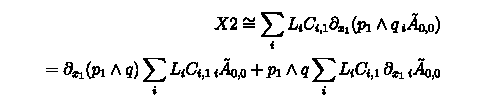

```mathematica
MaTeX["\\begin{aligned}X2\\cong\\sum_i L_iC_{i,1}\\partial_{x_1}(p_1\\wedge q\\,_i\\tilde{A}_{0,0})\\\\=\\partial_{x_1}(p_1\\wedge q)\\sum_i L_iC_{i,1}\\,_i\\tilde{A}_{0,0}+p_1\\wedge q\\sum_i L_iC_{i,1}\\,\\partial_{x_1}\\,_i\\tilde{A}_{0,0}\\end{aligned}"]
```

```mathematica
X2=0;

Do[X2+=-D[Wedge[p1,q]*A0hbarl[i][0,ol],x1]×L[i]×Cfhbar[i][1],{i,fromDiag,toDiag}];

X2=simplifiedForm@onShellP[X2];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X2/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
MaTeX["\\begin{aligned}X3\\cong-\\frac{1}{2}\\sum_iL_iC_{i,0}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})\\\\=-\\frac{1}{2}\\partial_{x_1}^2(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,q^2\\,_i\\tilde{A}_{0,0}-\\partial_{x_1}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\partial_{x_1}(q^2\\,_i\\tilde{A}_{0,0})-\\frac{1}{2}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\partial_{x_1}^2(q^2\\,_i\\tilde{A}_{0,0})\\\\-\\frac{1}{2}\\partial_{x_1}\\partial_{x_2}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\,_i\\tilde{A}_{0,0}-\\frac{1}{2}\\partial_{x_1}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\partial_{x_2}(q^2\\,_i\\tilde{A}_{0,0})-\\frac{1}{2}\\partial_{x_2}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\partial_{x_1}(q^2\\,_i\\tilde{A}_{0,0})-\\frac{1}{2}(p_1\\wedge q)\\sum_iL_iC_{i,0}\\,\\partial_{x_1}\\partial_{x_2}(q^2\\,_i\\tilde{A}_{0,0})\\end{aligned}"]
```

-Graphics-

```mathematica
Do[X306[n]=0,{n,0,6}];

Do[Do[X306[n]+=(-Binomial[2,n])/2 D[q⊙q×ToExpression["A0"<>ToString[i]<>"hbar"][0],{x1,n}]×ToExpression["L"<>ToString[i]]×ToExpression["C"<>ToString[i]<>"hbar"][0],{i,1,2}],{n,0,2}];
Do[Do[X306[2n+m+3]+=-1/2 D[q⊙q×ToExpression["A0"<>ToString[i]<>"hbar"][0],{x1,n},{x2,m}]×ToExpression["L"<>ToString[i]]×ToExpression["C"<>ToString[i]<>"hbar"][0],{i,1,2}],{n,0,1},{m,0,1}]
```

```mathematica
(*X3[0] and X3[3] are zero*)
X306[0] = 0;
X306[3]=0;
```

```mathematica
Do[X306[n]=onShellP[X306[n]],{n,0,6}]
```

```mathematica
X3=-(γ Wedge[p1,p2])/S X306[1]-Wedge[p1,q]×X306[2]-(γ Wedge[p1,p2])/S X306[4]+(m1^2 Wedge[p1,p2])/S X306[5]-Wedge[p1,q]×X306[6];
```

```mathematica
X3=0;

Do[X3+=1/2 L[i]×Cfhbar[i][0]*(D[D[Wedge[p1,q]*q⊙q*A0hbarl[i][0,ol],x1],x1]-D[D[Wedge[p1,q]*q⊙q*A0hbarl[i][0,ol],x2],x1]),{i,fromDiag,toDiag}];

X3=simplifiedForm@onShellP@X3;
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X3/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

```mathematica
MaTeX["X4\\cong\\,p_1\\wedge q\\sum_i\\,_i\\tilde{A}_{0,1}\\partial_{x_1}L_iC_{i,0}"]
```

-Graphics-

```mathematica
X4=0;

Do[X4+=-Wedge[p1,q]*A0hbarl[i][1,ol]×D[L[i]×Cfhbar[i][0],x1],{i,fromDiag,toDiag}];

X4=simplifiedForm@onShellP[X4];
```

```mathematica
-simplifiedForm[onShellP[Wedge[p1,q]*A0hbarl[4][1,1]×D[L[4]×Cfhbar[4][0],x1]]]
```

-(2 ⅈ γ (l⊙p1+l⊙p2) p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
D[L[4]×Cfhbar[4][0],x1]
```

-(γ (-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S))/((-ⅈ ϵ+l⊙p2) (ⅈ ϵ-l⊙p1+p1⊙q)^2)

```mathematica
Cfhbar[4][0]
```

γ

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X4/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
MaTeX["X5\\cong\\,p_1\\wedge q\\sum_i\\,_i\\tilde{A}_{0,0}\\partial_{x_1}L_iC_{i,1}"]
```

-Graphics-

```mathematica
s=0;
Do[s+=aWedgeDb[L[i]*Cf[i],p1,p1],{i,1,4}];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[simplifiedForm[onShellP[s]]/.{l->ρ l, ϵ->ρ ϵ}],ρ,-3]
```

```mathematica
-(γ ℏ q⊙q l⋀p1)/(2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(γ ℏ q⊙q l⋀p1)/(2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))
```

```mathematica
(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(ℏ p1⋀q)/(2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(ℏ p1⋀q)/(2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(ℏ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))
```

```mathematica
X5=0;

Do[X5+=-Wedge[p1,q]×A0hbarl[i][0,ol]×D[L[i]×Cfhbar[i][1],x1],{i,fromDiag,toDiag}];

X5=simplifiedForm@onShellP[X5];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X5/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

(2 ⅈ γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(2 ⅈ γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)+(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
MaTeX["X6\\cong-\\frac{1}{2}p_1\\wedge q\\sum_iq^2\\,_i\\tilde{A}_{0,0}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})L_iC_{i,0}"]
```

-Graphics-

```mathematica
X6=0;

Do[X6+=(Wedge[p1,q]×q⊙q)/2 A0hbarl[i][0,ol]×(D[D[L[i]×Cfhbar[i][0],x1],x1]-D[D[L[i]×Cfhbar[i][0],x2],x1]),{i,fromDiag,toDiag}];

X6=simplifiedForm@onShellP[X6];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X6/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

```mathematica
MaTeX["\\begin{aligned}X7\\cong-\\sum_i\\partial_{x_1}(L_iC_{i,0})\\partial_{x_1}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})\\\\=-\\partial_{x_1}(p_1\\wedge q)\\sum_iq^2\\,_i\\tilde{A}_{0,0}\\partial_{x_1}(L_iC_{i,0})-p_1\\wedge q\\sum_i\\partial_{x_1}(L_iC_{i,0})\\partial_{x_1}(q^2\\,_i\\tilde{A}_{0,0})\\end{aligned}"]
```

-Graphics-

```mathematica
X7=0;

Do[X7+=D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x1]×D[L[i]×Cfhbar[i][0],x1],{i,fromDiag,toDiag}];

X7=simplifiedForm@onShellP[X7];
```

```mathematica
X7=0;

Do[X7+=Wedge[p1,q]×D[q⊙q×A0[i]/.{ρ->1},x1]×D[L[i]×Cf[i],x1],{i,1,4}];

X7=simplifiedForm@onShellP[X7];
```

```mathematica
a=Total@Select[List@@Expand[X7/.l⊙l-2 l⊙q+q⊙q->qml2],Exponent[#,ℏ]<=1&];
```

```mathematica
b={};
Do[AppendTo[b,simplifiedForm[a[[i]]]],{i,1,Length[a]}];
ClearAll[a];
a=Total[b];
ClearAll[b];
```

```mathematica
b={};
Do[AppendTo[b,simplifyTerm[a[[i]]]],{i,1,Length[a]}];
ClearAll[a];
a=Total[b];
ClearAll[b];
```

```mathematica
Expand[Series[Coefficient[factorRho[a/.{l->ρ l,ϵ->ρ ϵ}],ρ,-3]/.{qml2->1/(Normal[Series[1/(ρ^2 l⊙l+q⊙q-2ρ l⊙q),{ρ,0,1}]]/.{ρ->1})},{ρ,0,1}]]
```

```mathematica
Expand[Series[Coefficient[factorRho[a/.{l->ρ l,ϵ->ρ ϵ}],ρ,-3]/.{qml2->1/(Normal[Series[1/(ρ^2 l⊙l+q⊙q-2ρ l⊙q),{ρ,0,1}]]/.{ρ->1})},{ρ,0,1}]]
```

0

```mathematica
simplifyTerm[Expand[simplifiedForm@Normal[Series[X7/.l⊙l-2 l⊙q+q⊙q->qml2,{ℏ,0,1}]]]]
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X7/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

```mathematica
MaTeX["\\begin{aligned}X8\\cong\\frac{1}{2}\\sum_i\\partial_{x_1}(L_iC_{i,0})\\partial_{x_2}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})\\\\=\\frac{1}{2}\\partial_{x_2}(p_1\\wedge q)\\sum_iq^2\\,_i\\tilde{A}_{0,0}\\partial_{x_1}(L_iC_{i,0})+\\frac{1}{2}p_1\\wedge q\\sum_i\\partial_{x_1}(L_iC_{i,0})\\partial_{x_2}(q^2\\,_i\\tilde{A}_{0,0})\\end{aligned}"]
```

-Graphics-

```mathematica
X8=0;

Do[X8+=-1/2 D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x2]×D[L[i]×Cfhbar[i][0],x1],{i,fromDiag,toDiag}];

X8=simplifiedForm@onShellP[X8];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X8/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

```mathematica
X8=0;

Do[X8+=-1/2 D[Wedge[p1,q]×q⊙q×(A0hbarl[i][0,ol]+ℏ*A0hbarl[i][1,ol]),x2]×D[L[i]×(Cfhbar[i][0]+ℏ*Cfhbar[i][1]),x1],{i,fromDiag,toDiag}];

X8=simplifiedForm@onShellP[X8];
```

```mathematica
X8=0;

Do[X8+=-1/2 D[Wedge[p1,q]×q⊙q×A0[i],x2]×D[L[i]×Cf[i],x1],{i,1,4}];

X8=simplifiedForm@onShellP[X8];
```

```mathematica
a=Total@Select[List@@Expand[X8/.{ρ->1}/.l⊙l-2 l⊙q+q⊙q->qml2],Exponent[#,ℏ]<=1&];
```

```mathematica
b={};
Do[AppendTo[b,simplifiedForm[a[[i]]]],{i,1,Length[a]}];
ClearAll[a];
a=Total[b];
ClearAll[b];
```

```mathematica
b={};
Do[AppendTo[b,simplifyTerm[a[[i]]]],{i,1,Length[a]}];
ClearAll[a];
a=Total[b];
ClearAll[b];
```

```mathematica
Coefficient[factorRho[a/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

-(ⅈ m1^2 γ^2 ℏ l⊙l q⊙q p1⋀p2)/(qml2 S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+(2 ⅈ m1^2 γ ℏ q⊙q p1⋀p2)/(qml2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(2 ⅈ m1^2 m2^2 γ^2 ℏ q⊙q p1⋀p2)/(qml2 S^2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(2 ⅈ m1^2 m2^2 γ^2 ℏ q⊙q p1⋀p2)/(qml2 S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(2 ⅈ m1^2 γ^3 ℏ q⊙q p1⋀p2)/(qml2 S^2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(2 ⅈ m1^2 γ ℏ q⊙q p1⋀p2)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(2 ⅈ m1^2 γ^3 ℏ q⊙q p1⋀p2)/(qml2 S^2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 ⅈ γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 ⅈ γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

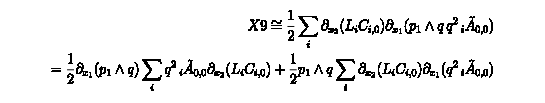

```mathematica
MaTeX["\\begin{aligned}X9\\cong\\frac{1}{2}\\sum_i\\partial_{x_2}(L_iC_{i,0})\\partial_{x_1}(p_1\\wedge q\\,q^2\\,_i\\tilde{A}_{0,0})\\\\=\\frac{1}{2}\\partial_{x_1}(p_1\\wedge q)\\sum_iq^2\\,_i\\tilde{A}_{0,0}\\partial_{x_2}(L_iC_{i,0})+\\frac{1}{2}p_1\\wedge q\\sum_i\\partial_{x_2}(L_iC_{i,0})\\partial_{x_1}(q^2\\,_i\\tilde{A}_{0,0})\\end{aligned}"]
```

```mathematica
X9=0;

Do[X9+=-1/2 D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x1]×D[L[i]×Cfhbar[i][0],x2],{i,fromDiag,toDiag}];

X9=simplifiedForm@onShellP[X9];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[X9/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

0

```mathematica
XSuml0=0;

Do[XSuml0+=ToExpression["X"<>ToString[n]], {n,1,9}];
```

```mathematica
YSuml0 = Y1+Y2+Y3;
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[(XSuml0+YSuml0)/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)-(8 ⅈ γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(4 ⅈ γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(4 ⅈ γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
MaTeX["\\begin{aligned} Y= \\sum_ip_1\\wedge\\partial_{p_1}A_{1,1}+\\frac{1}{2}\\sum_i(\\partial_{x_1}- \\partial_{x_2})(q^2\\,p_1\\wedge\\partial_{p_1}A_{1,0})\\\\=\\sum_ip_1\\wedge\\partial_{p_1}(L_iC_{i,0}\\,_iA_{0,1}+L_iC_{i,1}\\,_iA_{0,0})-\\frac{1}{2}\\sum_i(\\partial_{x_1}-\\partial_{x_2})(q^2\\,p_1\\wedge\\partial_{p_1}(L_iC_{i,0}\\,_iA_{0,0}))\\end{aligned}"]
```

-Graphics-

```mathematica
ol=1;
fromDiag=1;
toDiag=4;
```

```mathematica
Y1=0;

Do[Y1+=aWedgeDb[L[i]×Cfhbar[i][0],p1,p1]×A0hbarl[i][1,ol],{i,fromDiag,toDiag}];

Y1=simplifiedForm@onShellP@Y1;
```

```mathematica
Y2=0;

Do[Y2+=aWedgeDb[L[i]×Cfhbar[i][1]×A0hbarl[i][0,ol],p1,p1],{i,fromDiag,toDiag}];

Y2=simplifiedForm@onShellP@Y2;
```

```mathematica
Y3=0;

Do[Y3+=-1/2(D[q⊙q*aWedgeDb[L[i]×Chbar[i][0]×A0hbarl[i][0,ol],p1,p1],x1]-D[q⊙q*aWedgeDb[L[i]×Cfhbar[i][0]×A0hbarl[i][0,ol],p1,p1],x2]),{i,fromDiag,toDiag}];

Y3=simplifiedForm@onShellP@Y3;
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[Y1/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
-(2 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(6 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

```mathematica
X4=0;

Do[X4+=-Wedge[p1,q]*A0hbarl[i][1,ol]×D[L[i]×Cfhbar[i][0],x1],{i,fromDiag,toDiag}];

X4=simplifiedForm@onShellP[X4];
```

```mathematica
MaTeX["\\begin{aligned} R_2 = -\\partial_{x_1}(p_1\\wedge q\\,A_{1,1})+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,A_{1,0}))\\\\=-\\partial_{x_1}(p_1\\wedge q\\,L_i(C_{i,1}A_{0,0}+C_{i,0}A_{0,1}))+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,L_iC_{i,0}A_{0,0}))\\end{aligned}"]
```

-Graphics-

```mathematica
(*ol=0;
fromDiag=1;
toDiag=2;

ClearAll[X];
Do[X[i]=0;,{i,1,9}];

Do[X[1]+=D[Wedge[p1,q]*A0hbarl[i][1,ol],x1]×L[i]×Cfhbar[i][0];

X[2]+=D[Wedge[p1,q]*A0hbarl[i][0,ol],x1]×L[i]×Cfhbar[i][1];

X[3]+=-1/2 L[i]×Cfhbar[i][0]*(D[D[Wedge[p1,q]*q⊙q*A0hbarl[i][0,ol],x1],x1]-D[D[Wedge[p1,q]*q⊙q*A0hbarl[i][0,ol],x2],x1]);

X[4]+=Wedge[p1,q]*A0hbarl[i][1,ol]×D[L[i]×Cfhbar[i][0],x1];

X[5]+=Wedge[p1,q]×A0hbarl[i][0,ol]×D[L[i]×Cfhbar[i][1],x1];

X[6]+=(-Wedge[p1,q]×q⊙q)/2 A0hbarl[i][0,ol]×(D[D[L[i]×Cfhbar[i][0],x1],x1]-D[D[L[i]×Cfhbar[i][0],x2],x1]);

X[7]+=-D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x1]×D[L[i]×Cfhbar[i][0],x1];

X[8]+=1/2 D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x2]×D[L[i]×Cfhbar[i][0],x1];

X[9]+=1/2 D[Wedge[p1,q]×q⊙q×A0hbarl[i][0,ol],x1]×D[L[i]×Cfhbar[i][0],x2];
,{i,fromDiag,toDiag}];

Do[X[i]=simplifiedForm@onShellP[X[i]];,{i,1,9}];

XSum=0;
Do[XSum+=X[i],{i,1,9}];*)
```

```mathematica
ol=2;
fromDiag=1;
toDiag=4;

ClearAll[X];
Do[X[i]=0;,{i,1,3}];

Do[X[1]+=-D[Wedge[p1,q]×L[i]×Cfhbar[i][0]×A0hbarl[i][1,ol],x1];
X[2]+=-D[Wedge[p1,q]×L[i]×Cfhbar[i][1]×A0hbarl[i][0,ol],x1];
X[3]+=1/2 D[(D[q⊙q*Wedge[p1,q]×L[i]×Cfhbar[i][0]×A0hbarl[i][0,ol],x1]-D[q⊙q*Wedge[p1,q]×L[i]×Cfhbar[i][0]×A0hbarl[i][0,ol],x2]),x1],{i,fromDiag,toDiag}];

Do[X[i]=simplifiedForm@onShellP@X[i];,{i,1,3}];

XSum=0;
Do[XSum+=X[i],{i,1,3}];
```

```mathematica
ol=0;
fromDiag=1;
toDiag=4;

ClearAll[Z];
Do[Z[i]=0;,{i,1,3}];

Do[Z[1]+=aWedgeDb[L[i]×Cfhbar[i][0]×A0hbarl[i][1,ol],p1,p1];
Z[2]+=aWedgeDb[L[i]×Cfhbar[i][1]×A0hbarl[i][0,ol],p1,p1];
Z[3]+=-1/2(D[q⊙q*aWedgeDb[L[i]×Cfhbar[i][0]×A0hbarl[i][0,ol],p1,p1],x1]-D[q⊙q*aWedgeDb[L[i]×Cfhbar[i][0]×A0hbarl[i][0,ol],p1,p1],x2]),{i,fromDiag,toDiag}];

Do[Z[i]=simplifiedForm@onShellP@Z[i];,{i,1,3}];

ZSum=0;
Do[ZSum+=Z[i],{i,1,3}];
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[(XSum+ZSum)/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
cancelFactors@Coefficient[Expand@factorRho[(ZSum)/.{l->ρ l, ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
(4 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(4 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(6 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

```mathematica
(*ZSum: l^0, l*)
```

```mathematica
-(2 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(6 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

```mathematica
(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

```mathematica
(*XSum: l^0, l*)
```

```mathematica
(2 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(6 ⅈ γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

```mathematica
-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 ⅈ γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)
```

## First Pair

```mathematica
Bx1 = ((2p1+ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q+ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
Cx1 = ((2p1+ℏ q+ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙(q-l)-ℏ(q-l)⊙(q-l)-ⅈ ϵ));
```

```mathematica
B1C1 = Bx1+Cx1/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2};
```

```mathematica
B1C1
```

((ℏ^2 l⊙l+2 ℏ l⊙p1+2 ℏ l⊙p2-2 ℏ^2 l⊙q+4 p1⊙p2-4 ℏ p1⊙q) (ℏ^2 l⊙l+2 ℏ l⊙p1+2 ℏ l⊙p2+4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(qml2 (ⅈ ϵ+ℏ l⊙l+2 l⊙p1) (-ⅈ ϵ-qml2 ℏ+2 (-l⊙p2+p2⊙q)))+((-ℏ^2 l⊙l-2 ℏ l⊙p1+2 ℏ l⊙p2+4 p1⊙p2) (-ℏ^2 l⊙l-2 ℏ l⊙p1+2 ℏ l⊙p2-2 ℏ^2 l⊙q+4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(qml2 (ⅈ ϵ+ℏ l⊙l+2 l⊙p1) (-ⅈ ϵ-ℏ l⊙l+2 l⊙p2))

```mathematica
Do[Bx1hbar[n] = Coefficient[Normal[Series[Bx1, {ℏ,0,1}]],ℏ,n];
Cx1hbar[n] = Coefficient[Normal[Series[Cx1, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
simplifiedForm@Bx1hbar[0]
```

(4 (p1⊙p2)^2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
simplifiedForm@Cx1hbar[0]
```

-(4 (p1⊙p2)^2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2-p2⊙q) (l⊙l-2 l⊙q+q⊙q))

### R_2

```mathematica
MaTeX["\\begin{aligned}R_2 = -\\partial_{x_1}(p_1\\wedge q\\,(B_0+C_0))+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,(B_{-1}+C_{-1}))\\\\=p_1\\wedge q\\,\\left(-\\partial_{x_1}(B_0+C_0)+\\frac{1}{2}\\,\\partial_{x_1}^2(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_1}\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\+\\,\\partial_{x_1}(p_1\\wedge q)\\left(-\\,(B_0+C_0)+\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\-\\frac{1}{2}\\,\\partial_{x_2}(p_1\\wedge q)\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
R21D1 = -simplifiedForm[onShellP[D[Wedge[p1,q]*(Expand[(Bx1hbar[1]+Cx1hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q),x1]]];

R22D1=(D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x1],x1]-D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x2],x1])//.{(-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S)->1,((m2^2 p1⊙p1)/S-(γ p1⊙p2)/S)->-1,((γ p1⊙p2)/S-(m1^2 p2⊙p2)/S)->1,(-(γ p1⊙p2)/S+(m1^2 p2⊙p2)/S)->-1,((γ p1⊙p1)/S-(m1^2 p1⊙p2)/S)->0,(-(γ p1⊙p1)/S+(m1^2 p1⊙p2)/S)->0,(-(m2^2 p1⊙p2)/S+(γ p2⊙p2)/S)->0,((m2^2 p1⊙p2)/S-(γ p2⊙p2)/S)->0};
R22D1=1/2 simplifiedForm@onShellP[R22D1];
(*ClearAll[workspace1, workspace2];*)
```

```mathematica
R22D1=1/2(D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x1],x1]-D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x2],x1]);
```

```mathematica
R22D1 = simplifiedForm[onShellP[R22D1]];
```

```mathematica
R2D1=R21D1+R22D1;
```

```mathematica
R2D1=Collect[factorRho@(simplifiedForm[R2D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R2D1Div = Total@Select[List@@R2D1,Exponent[#,ρ]<-1&];
```

```mathematica
R2D1Div
```

```mathematica
R2D1Div=R2D1Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
Expand[simplifiedForm[onShellP[D[D[Bx1hbar[0]+Cx1hbar[0],x1],x1]-D[D[Bx1hbar[0]+Cx1hbar[0],x1],x2]]]]
```

```mathematica
Coefficient[Collect[factorRho[simplifyTerm[Expand[R22D1]]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ],ρ,-2]
```

-(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
C->(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))
```

```mathematica
B->-(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))
```

#### R_1

```mathematica
MaTeX["\\begin{aligned}R_1= (p_1\\wedge \\partial_{p_1})(B_0+C_0)-\\frac{1}{2}(\\partial_{x_1}-\\partial_{x_2})(q^2 (p_1\\wedge \\partial_{p_1})(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
R11D1 = simplifiedForm[onShellP[aWedgeDb[Expand[(Bx1hbar[1]+Cx1hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q, p1,p1]]];
R12D1 = -1/2 simplifiedForm[onShellP[D[q⊙q×aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1],x1]-D[q⊙q×aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1],x2]]];
```

```mathematica
simplifyTerm@Coefficient[Collect[factorRho@(Expand[R22D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-2]
```

0

```mathematica
R1D1=R11D1+R12D1;
```

```mathematica
R12D1
```

1/2 (-q⊙q ((8 γ^2 (-(m2^2 l⊙p1)/S+(γ l⊙p2)/S) l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 γ^2 (-(m2^2 l⊙p1)/S+(γ l⊙p2)/S) l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(16 γ (-(m2^2 l⊙p1)/S+(γ l⊙p2)/S) p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(16 γ (-(m2^2 l⊙p1)/S+(γ l⊙p2)/S) p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2))+q⊙q ((8 γ^2 ((γ l⊙p1)/S-(m1^2 l⊙p2)/S) l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 γ^2 ((γ l⊙p1)/S-(m1^2 l⊙p2)/S) l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))+(16 γ ((γ l⊙p1)/S-(m1^2 l⊙p2)/S) p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(16 γ ((γ l⊙p1)/S-(m1^2 l⊙p2)/S) p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))))

Singular terms

```mathematica
S1 = simplifiedForm@onShellP[aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1]]
```

(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
simplifiedForm[expr_]:=expr//.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1}/.{ϵ->2ϵ}/.{(coef1_ ϵ+coef2_ l⊙p1)^(n_)->(coef2)^n*(ϵ*coef1/coef2+l⊙p1)^n,(coef1_ ϵ+coef2_ l⊙p2)^(n_)->(coef2)^n*(ϵ*coef1/coef2+l⊙p2)^n}
```

```mathematica
S2=-simplifiedForm@onShellP[Expand[D[Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x1]]]/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
S1+S2
```

(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
R1D1=Collect[factorRho@(simplifiedForm[R1D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R1D1Div = Total@Select[List@@R1D1,Exponent[#,ρ]<-1&];
```

```mathematica
R1D1Div=R1D1Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

((2 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(2 γ^2 q⊙q l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(4 γ q⊙q p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2))/ρ^3+(-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

```mathematica
Collect[factorRho[simplifyTerm[R11D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ]
```

((2 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2))/ρ^3+1/ρ((2 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-(4 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(4 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-(4 p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p2))-(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(4 p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p2))+(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)))+(-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

## Second Pair

### R_2 for the last two diagrams

```mathematica
Bx2 = ((2p1+ℏ q-ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+2ℏ q-ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙(q-l)+ℏ (q-l)⊙(q-l)+ⅈ ϵ)(2p2⊙(q-l)-ℏ (q-l)⊙(q-l)-ⅈ ϵ));
Cx2 = ((2p1+2ℏ q-ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q-ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙(q-l)+ℏ (q-l)⊙(q-l)+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
```

```mathematica
B2C2 = Bx2+Cx2;
```

```mathematica
Do[Bx2hbar[n] = Coefficient[Normal[Series[Bx2, {ℏ,0,1}]],ℏ,n];
Cx2hbar[n] = Coefficient[Normal[Series[Cx2, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
Distribute@simplifiedForm@B2xhbar[1]
```

(16 (p1⊙p2)^2)/((2 ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2 (-2 ⅈ ϵ-2 l⊙p2+2 p2⊙q))+((8 p1⊙p2 (l⊙p1-l⊙p2-p1⊙q+p2⊙q)+4 p1⊙p2 (2 l⊙p1-2 l⊙p2-4 p1⊙q+4 p2⊙q))/(-2 ⅈ ϵ-2 l⊙p2+2 p2⊙q)+(16 (p1⊙p2)^2 (-l⊙l+2 l⊙q-q⊙q))/(2 ϵ-2 ⅈ l⊙p2+2 ⅈ p2⊙q)^2)/((2 ⅈ ϵ-2 l⊙p1+2 p1⊙q) (l⊙l-2 l⊙q+q⊙q))

```mathematica
Distribute@simplifiedForm@C2xhbar[1]
```

(8 (p1⊙p2)^2)/((-ⅈ ϵ+l⊙p2) (2 ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2)+(4 p1⊙p2 ((l⊙l p1⊙p2)/(-ⅈ ϵ+l⊙p2)^2-(l⊙p1+l⊙p2-2 p2⊙q)/(-ⅈ ϵ+l⊙p2))-(4 p1⊙p2 (l⊙p1+l⊙p2+p1⊙q-p2⊙q))/(-ⅈ ϵ+l⊙p2))/((2 ⅈ ϵ-2 l⊙p1+2 p1⊙q) (l⊙l-2 l⊙q+q⊙q))

```mathematica
MaTeX["\\begin{aligned}R_2 = -\\partial_{x_1}(p_1\\wedge q\\,(B_0+C_0))+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,(B_{-1}+C_{-1}))\\\\=p_1\\wedge q\\,\\left(-\\partial_{x_1}(B_0+C_0)+\\frac{1}{2}\\,\\partial_{x_1}^2(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_1}\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\+\\,\\partial_{x_1}(p_1\\wedge q)\\left(-\\,(B_0+C_0)+\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\-\\frac{1}{2}\\,\\partial_{x_2}(p_1\\wedge q)\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
R21D2 = -simplifiedForm[onShellP[D[Wedge[p1,q]*(Expand[(Bx2hbar[1]+Cx2hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q),x1]]];

R22D2=D[q⊙q×Wedge[p1,q]*(Bx2hbar[0]+Cx2hbar[0]),x1];
workspace=D[R22D2,x2];
R22D2=D[R22D2,x1]-workspace;
R22D2=1/2 simplifiedForm[onShellP[R22D2]];
ClearAll[workspace];
```

```mathematica
R2D2=R21D2+R22D2;
```

```mathematica
R2D2=Collect[factorRho@(R2D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R2D2Div = Total@Select[List@@R2D2,Exponent[#,ρ]<-1&];
```

```mathematica
R2D2Div=R2D2Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2};
```

```mathematica
Coefficient[R1D2Div+R2D2Div,ρ,-4]
```

(8 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(8 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))

```mathematica
Collect[factorRho[simplifyTerm[Expand[R11D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]]/.{l->ρ l,ϵ->ρ ϵ}],ρ]
```

(-(2 γ^2 l⊙l l⋀p1)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-(4 γ l⊙l p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)+(4 p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p2))+(4 p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p2)))/ρ+1/ρ^3(-(4 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)))+(-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2)))/ρ^4+(-(2 γ^2 l⊙l p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+(6 γ p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(2 γ p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

```mathematica
R22D2=1/2(D[D[q⊙q×Wedge[p1,q]*(Bx2hbar[0]+Cx2hbar[0]),x1],x1]-D[D[q⊙q×Wedge[p1,q]*(Bx2hbar[0]+Cx2hbar[0]),x2],x1]);
```

```mathematica
R22D2 = simplifiedForm[onShellP[R22D2]];
```

```mathematica
R22 = R22D1+R22D2;
```

### R1 for the last two diagrams

```mathematica
MaTeX["\\begin{aligned}R_1= (p_1\\wedge \\partial_{p_1})(B_0+C_0)-\\frac{1}{2}(\\partial_{x_1}-\\partial_{x_2})(q^2 (p_1\\wedge \\partial_{p_1})(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
B2xhbar[1]
```

(((8 p1⊙p2 (l⊙p1-l⊙p2-p1⊙q+p2⊙q)+4 p1⊙p2 (2 l⊙p1-2 l⊙p2-4 p1⊙q+4 p2⊙q))/(-ⅈ ϵ-2 l⊙p2+2 p2⊙q)+(16 (p1⊙p2)^2 (-l⊙l+2 l⊙q-q⊙q))/(ϵ-2 ⅈ l⊙p2+2 ⅈ p2⊙q)^2)/(ⅈ ϵ-2 l⊙p1+2 p1⊙q)+(16 (p1⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))/((ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2 (-ⅈ ϵ-2 l⊙p2+2 p2⊙q)))/(l⊙l-2 l⊙q+q⊙q)

```mathematica
(*R11D2 = aWedgeDb[B2xhbar[1]+C2xhbar[1], p1,p1];
R12D2 = -1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x2];*)
```

```mathematica
R11D2=aWedgeDb[Expand[(Bx2hbar[1]+Cx2hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.{qml2->l⊙l-2 l⊙q+q⊙q},p1,p1];
R12D2 = -1/2 D[q⊙q×aWedgeDb[Bx2hbar[0]+Cx2hbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[Bx2hbar[0]+Cx2hbar[0], p1,p1],x2];

R11D2=onShellP[R11D2];
R12D2 =onShellP[R12D2];

R11D2=simplifiedForm@R11D2;
R12D2=simplifiedForm@R12D2;
R1D2=R11D2+R12D2;
```

```mathematica
Coefficient[Collect[factorRho@(simplifyTerm[Expand[simplifiedForm[R11D2]]]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-4]
```

-(4 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^3 (-2 ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^2 (2 ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^3 (2 ⅈ ϵ+l⊙p2))

```mathematica
R1D2=simplifiedForm@R1D2;
```

```mathematica
R1D2=Collect[factorRho@(R1D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R1D2Div = Total@Select[List@@R1D2,Exponent[#,ρ]<-1&];
```

```mathematica
R1D2Div=R1D2Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2};
```

```mathematica
-(4 m2^2 γ^2 l⊙p2 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1)^2)

```mathematica
Coefficient[R1D2Div+R2D2Div,ρ,-2]
```

(4 γ^3 p1⋀q)/(qml2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)

```mathematica
RD2LogDiv=(8π ⅈ γ^3 p1⋀q δ[l⊙p2])/(qml2 S (-ⅈ ϵ+l⊙p1))-(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2);
```

```mathematica
S2
```

-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
S3 = simplifiedForm@onShellP[aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1]]
```

-(8 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(2 ⅈ γ^2 (-2 ⅈ l⋀p1-2 ⅈ p1⋀q))/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(2 γ^2 (2 l⋀p1+2 p1⋀q))/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
S4=-Expand[simplifiedForm@onShellP[D[Wedge[p1,q]*(B2xhbar[0]+C2xhbar[0]),x1]]]/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
Expand[S1+S2+S3+S4]
```

```mathematica
simplifyTerm[Total@Select[List@@Expand[R12D1+R12D2],ContainsAll[List@@Numerator[#],{p1⋀q}]&]]
```

-(4 m2^2 γ^2 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(4 γ^3 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 m2^2 γ^2 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 γ^3 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(2 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
simplifyTerm[Total@Select[List@@Expand[R22D1+R22D2],ContainsAll[List@@Numerator[#],{p1⋀q}]&]]
```

(4 m2^2 γ^2 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 m2^2 γ^2 q⊙q p1⋀q)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 γ^3 q⊙q p1⋀q)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(4 γ^3 q⊙q p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)+(4 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(2 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))+(4 γ^2 q⊙q p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

### R_2 for first two diagrams

```mathematica
Bx = ((2p1+ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q+ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
Cx = ((2p1+ℏ q+ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙(q-l)-ℏ(q-l)⊙(q-l)-ⅈ ϵ));
```

```mathematica
BC = Bx+Cx;
```

```mathematica
Do[Bxhbar[n] = Coefficient[Normal[Series[Bx, {ℏ,0,1}]],ℏ,n];
Cxhbar[n] = Coefficient[Normal[Series[Cx, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
R21 = -D[Bxhbar[1]+Cxhbar[1],x1];
R22 = 1/2 D[q⊙q×(Bxhbar[0]+Cxhbar[0]),{x1,2}];
R23 = -1/2 D[q⊙q×(Bxhbar[0]+Cxhbar[0]),{x1,1},{x2,1}];
```

```mathematica
R21=onShellP[R21];
R22=onShellP[R22];
R23=onShellP[R23];
```

```mathematica
Rpwq = R21+R22+R23;
```

```mathematica
factorRho[exp_]:=exp/.{(expr_Plus)^(n_):>Factor[expr]^n/;ContainsAll[Variables[expr], {ϵ,l⊙p1}]||ContainsAll[Variables[expr], {ϵ,l⊙p2}]}
```

```mathematica
Coefficient[factorRho@Expand[simplifiedForm[Rpwq]/.{l⊙l-2 l⊙q+q⊙q->qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
R2D1Div=Wedge[p1,q]/qml2((2 γ)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(6 γ)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(8π ⅈ γ^3 δ[l⊙p2])/(S (ⅈ ϵ+l⊙p1)))+(Wedge[p1,q]q⊙q)/(S qml2^2)((4 γ^3)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2)/(ⅈ ϵ+l⊙p2)^2+(8π ⅈ m2^2 γ^2 δ[l⊙p2])/(ⅈ ϵ+l⊙p1));
```

### R_1 for the first two diagrams

```mathematica
R11 = aWedgeDb[Bxhbar[1]+Cxhbar[1], p1,p1];
R12 = -1/2 D[q⊙q×aWedgeDb[Bxhbar[0]+Cxhbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[Bxhbar[0]+Cxhbar[0], p1,p1],x2];
```

```mathematica
R11=onShellP[R11];
R12 =onShellP[R12];
```

```mathematica
R1D1Log=Coefficient[factorRho@Expand[simplifiedForm[R11+R12]/.{l⊙l-2 l⊙q+q⊙q->qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
RD1LogDiv=Expand[R1D1Log+R2D1Div]
```

(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (ⅈ ϵ+l⊙p1))+(8 ⅈ m2^2 π γ^2 q⊙q p1⋀q δ[l⊙p2])/(qml2^2 S (ⅈ ϵ+l⊙p1))

```mathematica
RD1LogDiv+RD2LogDiv
```

```mathematica
-(8π ⅈ γ^3 q⊙q p1⋀q δ[l⊙p1])/(qml2^2 S (-ⅈ ϵ+l⊙p1))+(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (-ⅈ ϵ+l⊙p1))-(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (ⅈ ϵ+l⊙p1))+(8 ⅈ m2^2 π γ^2 q⊙q p1⋀q δ[l⊙p2])/(qml2^2 S (ⅈ ϵ+l⊙p1))
```

```mathematica
Coefficient[Collect[factorRho@(R1D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-4]
```

```mathematica
R1D2->-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(2 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))
```

```mathematica
R2D2->(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))
```

```mathematica
Normal[Series[1/(l⊙l-2 l⊙q+q⊙q)/.{l->ρ l},{ρ,0,2}]]
```

(2 ρ l⊙q)/(q⊙q)^2+1/(q⊙q)+(ρ^2 (4 (l⊙q)^2-l⊙l q⊙q))/(q⊙q)^3

```mathematica
wsp = q⊙q*aWedgeDb[(Bx1hbar[0]+Bx2hbar[0]+Cx1hbar[0]+Cx2hbar[0]),p1,p1];

t1=Expand[simplifiedForm[onShellP[D[wsp,x1]-D[wsp,x2]]]];
ClearAll[wsp];
wsp = List@@t1;
ClearAll[t1];
t1={};
Do[AppendTo[t1,simplifyTerm[wsp[[i]]]],{i,1,Length[wsp]}];
t1=Total[t1];
ClearAll[wsp];
```

```mathematica
wsp = q⊙q*Wedge[p1,q]*(Bx1hbar[0]+Bx2hbar[0]+Cx1hbar[0]+Cx2hbar[0]);

t2=Expand[simplifiedForm[onShellP[D[D[wsp,x1]-D[wsp,x2],x1]]]];
ClearAll[wsp];
wsp = List@@t2;
ClearAll[t2];
t2={};
Do[AppendTo[t2,simplifyTerm[wsp[[i]]]],{i,1,Length[wsp]}];
t2=Total[t2];
ClearAll[wsp];
```

```mathematica
t1=factorRho[t1/.{l->ρ l, ϵ->ρ ϵ}];
t2=factorRho[t2/.{l->ρ l, ϵ->ρ ϵ}];
```

```mathematica
t1=t1/.{(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,2}]]};
t2=t2/.{(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,2}]]};
```

```mathematica
Coefficient[Expand[t1],ρ,-2]-Coefficient[Expand[t2],ρ,-2]
```

-(16 γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2) q⊙q)-(8 γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 γ^2 l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 γ^2 l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2) q⊙q)-(16 γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)+(8 γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) q⊙q)-(16 γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(8 γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 γ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)-(8 γ^3 l⊙q p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2 q⊙q)+(16 γ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)-(8 γ^3 l⊙q p1⋀p2)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) q⊙q)-(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(8 γ^3 p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)-(8 γ^3 p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
s1=simplifyTerm@Expand[simplifiedForm[onShellP[aWedgeDb[(Bx1hbar[1]+Bx2hbar[1]+Cx1hbar[1]+Cx2hbar[1]),p1,p1]]]];
s2=simplifyTerm@Expand[simplifiedForm[onShellP[D[Wedge[p1,q]*(Bx1hbar[1]+Bx2hbar[1]+Cx1hbar[1]+Cx2hbar[1]),x1]]]];
```

```mathematica
s1=factorRho[s1/.{l->ρ l, ϵ->ρ ϵ}];
s2=factorRho[s2/.{l->ρ l, ϵ->ρ ϵ}];
```

```mathematica
s1=s1/.{(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,3}]]};
s2=s2/.{(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,3}]]};
```

```mathematica
Coefficient[Expand[s1],ρ,-2]
```

-(2 γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2 q⊙q)+(6 γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(6 γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
Coefficient[Expand[s2],ρ,-2]
```

-(2 γ^2 l⊙l p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2 q⊙q)+(6 γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 γ p1⋀q)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) q⊙q)-(2 γ p1⋀q)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)+(6 γ p1⋀q)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) q⊙q)

```mathematica
sum=0;
Do[sum+=L[i]Cf[i](A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2]),{i,1,4}]
```

```mathematica
sum=0;
Do[sum+=L[i]Cf[i]A0[i],{i,1,4}]
```

```mathematica
Expand[simplifyTerm[Expand[simplifiedForm[sum]]]/.{(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,2}]]}/.{ρ->1}]
```

```mathematica
simplifyTerm[Expand[Expand[simplifiedForm[Bx1hbar[1]+Bx2hbar[0]+Cx1hbar[0]+Cx2hbar[1]]]/.{l->ρ l,ϵ->ρ ϵ}/.{Power[(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),-1]->1/Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,2}]]}/.{ρ->1}]]-simplifyTerm[simplifiedForm[Expand[sum]]]
```

```mathematica
simplifyTerm[simplifiedForm[Expand[sum]]]
```

```mathematica
a=simplifyTerm[simplifiedForm[factorRho[Expand[Expand[Bx1hbar[1]]/.{l->ρ l,ϵ->ρ ϵ}/.{Power[(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),-1]->Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),{ρ,0,2}]],Power[(ρ^2 l⊙l-2 ρ l⊙q+q⊙q),-2]->Normal[Series[1/(ρ^2 l⊙l-2 ρ l⊙q+q⊙q)^2,{ρ,0,2}]]}]]]/.{ρ->1}];
```

```mathematica
b=simplifyTerm[simplifiedForm[Expand[(L[i]Cf[i](A0hbarl[i][0,0]+A0hbarl[i][0,1]+A0hbarl[i][0,2]+ℏ A0hbarl[i][1,0]+ℏ A0hbarl[i][1,1]+ℏ A0hbarl[i][1,2])/.{i->1})]]];
```

```mathematica
Length[a]
Length[Coefficient[b,ℏ,1]]
Length[factorRho@(Expand[ⅈ a]-Coefficient[b,ℏ,1])/.p1⊙p2->γ]
```

24

28

4

```mathematica
(Expand[ⅈ a]-Coefficient[b,ℏ,0])/.p1⊙p2->γ
```

0

```mathematica
factorRho[Expand[ⅈ a]/.p1⊙p2->γ/.{l->ρ l,ϵ->ρ ϵ}]
```

```mathematica
Complement[List@@factorRho[Coefficient[b,ℏ,1]/.p1⊙p2->γ/.{l->ρ l,ϵ->ρ ϵ}],List@@factorRho[Expand[ⅈ a]/.p1⊙p2->γ/.{l->ρ l,ϵ->ρ ϵ}]]
```

{(8 ⅈ γ ρ (l⊙q)^2)/((ⅈ ϵ+l⊙p1) (q⊙q)^3),-(8 ⅈ γ ρ (l⊙q)^2)/((-ⅈ ϵ+l⊙p2) (q⊙q)^3),-(2 ⅈ γ ρ l⊙l)/((ⅈ ϵ+l⊙p1) (q⊙q)^2),(2 ⅈ γ ρ l⊙l)/((-ⅈ ϵ+l⊙p2) (q⊙q)^2)}

```mathematica
Complement[List@@factorRho[Expand[ⅈ a]/.p1⊙p2->γ/.{l->ρ l,ϵ->ρ ϵ}],List@@factorRho[Coefficient[b,ℏ,1]/.p1⊙p2->γ/.{l->ρ l,ϵ->ρ ϵ}]]
```

{(16 ⅈ γ ρ (l⊙q)^2)/((ⅈ ϵ+l⊙p1) (q⊙q)^3),-(16 ⅈ γ ρ (l⊙q)^2)/((-ⅈ ϵ+l⊙p2) (q⊙q)^3),-(4 ⅈ γ ρ l⊙l)/((ⅈ ϵ+l⊙p1) (q⊙q)^2),(4 ⅈ γ ρ l⊙l)/((-ⅈ ϵ+l⊙p2) (q⊙q)^2)}

```mathematica
Coefficient[Expand[simplifyTerm[Expand[L[1]Cf[1]]](A0hbar[1][0]+ℏ A0hbar[1][1])],ℏ,1]
```

```mathematica
Expand[L[1]Cf[1]]
```

(γ ℏ l⊙l)/(2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-(γ ℏ l⊙l)/(2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+γ/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(ℏ l⊙p1)/(2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(ℏ l⊙p2)/(2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))

## One Loop: Calculation 3

```mathematica
MaTeX["\\begin{aligned}Q_1=J_1|_{O(l^{-2}),O(\\hbar^0)},\\;\\;Q_2=J_1|_{O(l^{-2}),O(\\hbar)},\\\\Q_3=J_2|_{O(l^{-2}),O(\\hbar^0)}\\\\Q_4=J_3|_{O(l^{-2}),O(\\hbar^0)},\\;\\;Q_5=J_3|_{O(l^{-2}),O(\\hbar)}\\\\Q_6=J_4|_{O(l^{-2}),O(\\hbar^0)}\\\\Q_7=J_1|_{O(l^{-3}),O(\\hbar^0)},\\;\\;Q_8=J_1|_{O(l^{-3}),O(\\hbar)},\\\\Q_9=J_2|_{O(l^{-3}),O(\\hbar^0)}\\\\Q_{10}=J_3|_{O(l^{-3}),O(\\hbar^0)},\\;\\;Q_{11}=J_3|_{O(l^{-3}),O(\\hbar)}\\\\Q_{12}=J_4|_{O(l^{-3}),O(\\hbar^0)}\\\\Q_{13}=J_1|_{O(l^{-4}),O(\\hbar^0)},\\;\\;Q_{14}=J_1|_{O(l^{-4}),O(\\hbar)},\\\\Q_{15}=J_2|_{O(l^{-4}),O(\\hbar^0)}\\\\Q_{16}=J_3|_{O(l^{-4}),O(\\hbar^0)},\\;\\;Q_{17}=J_3|_{O(l^{-4}),O(\\hbar)}\\\\Q_{18}=J_4|_{O(l^{-4}),O(\\hbar^0)}\\end{aligned}"]
```

-Graphics-

```mathematica
MaTeX["J1=\\sum_iL_iC_i,\\;\\;J2=\\partial_{\\Delta x}\\sum_iL_iC_i,\;\;J3=p_1\\wedge \\partial p_1\\sum_iL_iC_i-p_1\\wedge q\\partial_{x_1}\\sum_iL_iC_i,\\\\J4=\\partial_{\\Delta x}\\Big(p_1\\wedge \\partial p_1\\sum_iL_iC_i-p_1\\wedge q\\partial_{x_1}\\sum_iL_iC_i\\Big)"]
```

-Graphics-

```mathematica
ClearAll[sum];
sum=0;
Do[sum+=L[i]*Cf[i]/.{γ->p1⊙p2},{i,1,4}]
```

```mathematica
ClearAll[J1,J2,J3,J4];
J1=sum;
J2=delx[J1];
J3=aWedgeDb[sum,p1,p1]-p1⋀q*D[sum,x1];
J4=delx[J3];

J1=simplifiedForm[onShellP[J1]];
J2=simplifiedForm[onShellP[J2]];
J3=simplifiedForm[onShellP[J3]];
J4=simplifiedForm[onShellP[J4]];
```

```mathematica
ClearAll[J1lm2,J2lm2,J3lm2,J4lm2];
J1lm2=extractLog[J1,-2];
J2lm2=extractLog[J2,-2];
J3lm2=extractLog[J3,-2];
J4lm2=extractLog[J4,-2];
```

```mathematica
ClearAll[J1lm3,J2lm3,J3lm3,J4lm3];
J1lm3=extractLog[J1,-3];
J2lm3=extractLog[J2,-3];
J3lm3=extractLog[J3,-3];
J4lm3=extractLog[J4,-3];
```

```mathematica
ClearAll[J1lm4,J2lm4,J3lm4,J4lm4];
J1lm4=extractLog[J1,-4];
J2lm4=extractLog[J2,-4];
J3lm4=extractLog[J3,-4];
J4lm4=extractLog[J4,-4];
```

```mathematica
MaTeX["\\begin{aligned}R_{(1)}=\\frac{1}{\\hbar}\\Big(p_1\\wedge \\partial p_1A_0-\\partial_{x_1}(p_1\\wedge q\,A_0)\\Big)J1-\\frac{1}{2}\\partial_{\\Delta x}\\Big(q^2\\,p_1\\wedge \\partial p_1A_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,A_0)\\Big)J1\\\\-\\frac{1}{2}\\Big(q^2\\,p_1\\wedge \\partial p_1A_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,A_0)\\Big)J2\\\\+\\frac{1}{\\hbar}A_0J_3-\\frac{1}{2}\\partial_{\\Delta x}(q^2\\,A_0)J_3\\\\-\\frac{1}{2}q^2\\,A_0\\,J_4\\\\-\\frac{1}{\\hbar}l^{(1)}\\Big[J_3\\partial_q\,A_0+J_1(p_1\\partial_{p_1}\\,\\partial_qA_0-\\partial_{x_1}(p_1\\wedge q\,\\partial_q\\,A_0))\\Big]\\\\+\\frac{1}{2}\\,l^{(1)}\\Big[J_1\\,\\partial_{\\Delta x}(q^2\\,p_1\\wedge\\partial_{p_1}\\,\\partial_qA_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,\\partial_q\\,A_0))+J_2(q^2\\,p_1\\wedge\\partial_{p_1}\\,\\partial_qA_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,\\partial_q\\,A_0))\\\\+J_3\\,\\partial_{\\Delta x}(q^2\\,\\partial_q\,A_0)+J_4\\,q^2\\,\\partial_q\,A_0\\Big]\\\\+\\frac{1}{2\\hbar}l^{(2)}\\Big[J_3\\partial_q^2\,A_0+J_1(p_1\\partial_{p_1}\\,\\partial_q^2A_0-\\partial_{x_1}(p_1\\wedge q\,\\partial_q^2\\,A_0))\\Big]\\\\-\\frac{1}{4}\\,l^{(2)}\\Big[J_1\\,\\partial_{\\Delta x}(q^2\\,p_1\\wedge\\partial_{p_1}\\,\\partial_q^2A_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,\\partial_q^2\\,A_0))+J_2(q^2\\,p_1\\wedge\\partial_{p_1}\\,\\partial_q^2A_0-\\partial_{x_1}(q^2\\,p_1\\wedge q\,\\partial_q^2\\,A_0))\\\\+J_3\\,\\partial_{\\Delta x}(q^2\\,\\partial_q^2\,A_0)+J_4\\,q^2\\,\\partial_q^2\,A_0\\Big]\\end{aligned}"]
```

-Graphics-

```mathematica
J4lm3
```

-(2 γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(γ l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(2 γ l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(6 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^4 (-ⅈ ϵ+l⊙p2))-(2 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^3)+(2 γ ℏ l⊙q l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^3)+(4 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2)^2)-(6 γ ℏ l⊙q l⋀p1)/((-ⅈ ϵ+l⊙p1)^4 (ⅈ ϵ+l⊙p2))-(p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)+(2 ℏ l⊙q p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^3)+(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(2 ℏ l⊙q p1⋀p2)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(m2^2 γ ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ^2 ℏ p1⋀q)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(m2^2 γ ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(γ^2 ℏ p1⋀q)/(S (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
ClearAll[B0C0, B1C1];
B0C0 = Bx1hbar[0]+Bx2hbar[0]+Cx1hbar[0]+Cx2hbar[0];
B1C1 = Bx1hbar[1]+Bx2hbar[1]+Cx1hbar[1]+Cx2hbar[1];
```

```mathematica
simplifiedForm[B0C0/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]
```

(4 (p1⊙p2)^2)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 (p1⊙p2)^2)/(qml2 (-ⅈ ϵ+l⊙p2) (-ⅈ ϵ+l⊙p1-p1⊙q))-(4 (p1⊙p2)^2)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2-p2⊙q))+(4 (p1⊙p2)^2)/(qml2 (-ⅈ ϵ+l⊙p1-p1⊙q) (ⅈ ϵ+l⊙p2-p2⊙q))

```mathematica
simplifiedForm[B1C1/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]
```

(-(2 qml2 (p1⊙p2)^2)/((-ⅈ ϵ+l⊙p2) (-ⅈ ϵ+l⊙p1-p1⊙q)^2)-(4 p1⊙p2 ((l⊙l p1⊙p2)/(-ⅈ ϵ+l⊙p2)^2-(l⊙p1+l⊙p2-2 p2⊙q)/(-ⅈ ϵ+l⊙p2))-(4 p1⊙p2 (l⊙p1+l⊙p2+p1⊙q-p2⊙q))/(-ⅈ ϵ+l⊙p2))/(2 (-ⅈ ϵ+l⊙p1-p1⊙q)))/qml2+1/qml2(4 p1⊙p2 ((-2 l⊙p1+2 l⊙p2)/(4 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+4 ((l⊙l)/(8 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-(l⊙l)/(8 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))) p1⊙p2)-(2 p1⊙p2 (l⊙p1-l⊙p2+p1⊙q-p2⊙q))/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)))+((2 qml2 (p1⊙p2)^2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2-p2⊙q)^2)-(4 p1⊙p2 (-(l⊙l p1⊙p2)/(ⅈ ϵ+l⊙p1)^2+(l⊙p1+l⊙p2-2 p1⊙q)/(ⅈ ϵ+l⊙p1))+(4 p1⊙p2 (l⊙p1+l⊙p2-p1⊙q+p2⊙q))/(ⅈ ϵ+l⊙p1))/(2 (ⅈ ϵ+l⊙p2-p2⊙q)))/qml2+((2 qml2 (p1⊙p2)^2)/((-ⅈ ϵ+l⊙p1-p1⊙q)^2 (ⅈ ϵ+l⊙p2-p2⊙q))-((4 qml2 (p1⊙p2)^2)/(ⅈ ϵ+l⊙p2-p2⊙q)^2-(8 p1⊙p2 (l⊙p1-l⊙p2-p1⊙q+p2⊙q)+4 p1⊙p2 (2 l⊙p1-2 l⊙p2-4 p1⊙q+4 p2⊙q))/(2 (ⅈ ϵ+l⊙p2-p2⊙q)))/(2 (-ⅈ ϵ+l⊙p1-p1⊙q)))/qml2

```mathematica
Coefficient[Expand[simplifiedForm[B1C1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}],1/((-ⅈ ϵ+l⊙p1-p1⊙q) (ⅈ ϵ+l⊙p2-p2⊙q)),1]
```

(4 l⊙p1 p1⊙p2)/qml2-(4 l⊙p2 p1⊙p2)/qml2-(6 p1⊙p2 p1⊙q)/qml2+(6 p1⊙p2 p2⊙q)/qml2

```mathematica
ClearAll[R1B1C1];
R1B1C1=simplifyTerm[Expand[simplifiedForm[onShellP[aWedgeDb[B1C1,p1,p1]/l⊙l]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/4]];

ClearAll[R1B1C1p1q,R1B1C1p1p2,R1B1C1p1l];
R1B1C1p1q=Coefficient[R1B1C1,p1⋀q,1];
R1B1C1p1p2=Coefficient[R1B1C1,p1⋀p2,1];
R1B1C1p1l=Coefficient[R1B1C1,l⋀p1,1];
```

```mathematica
ClearAll[R1B0C0];
R1B0C0 = simplifyTerm[Expand[simplifiedForm[onShellP[delx[-q⊙q*aWedgeDb[B0C0,p1,p1]]/(8*l⊙l)]]]];

ClearAll[R1B0C0p1q,R1B0C0p1p2,R1B0C0p1l];
R1B0C0p1q=Coefficient[R1B0C0,p1⋀q,1];
R1B0C0p1p2=Coefficient[R1B0C0,p1⋀p2,1];
R1B0C0p1l=Coefficient[R1B0C0,l⋀p1,1];
```

```mathematica
ClearAll[R2B1C1];
R2B1C1 = simplifyTerm[Expand[simplifiedForm[onShellP[D[-p1⋀q*(Expand[B1C1/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.{qml2->l⊙l-2 l⊙q+q⊙q}),x1]/(4*l⊙l)]]]];

ClearAll[R2B1C1p1q,R2B1C1p1p2,R2B1C1p1l];
R2B1C1p1q=Coefficient[R2B1C1,p1⋀q,1];
R2B1C1p1p2=Coefficient[R2B1C1,p1⋀p2,1];
R2B1C1p1l=Coefficient[R2B1C1,l⋀p1,1];
```

```mathematica
ClearAll[R2B0C0];
R2B0C0 = simplifyTerm[Expand[simplifiedForm[onShellP[delx[D[q⊙q*p1⋀q*B0C0,x1]]/(8*l⊙l)]]]];

ClearAll[R2B0C0p1q,R2B0C0p1p2,R2B0C0p1l];
R2B0C0p1q=Coefficient[R2B0C0,p1⋀q,1];
R2B0C0p1p2=Coefficient[R2B0C0,p1⋀p2,1];
R2B0C0p1l=Coefficient[R2B0C0,l⋀p1,1];
```

```mathematica
R1B0C0p1p2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

(γ q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(m1^2 γ^2 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+(γ q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ q⊙q)/(qml2 l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(γ q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(m1^2 γ^2 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
R2B0C0p1p2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

-(m1^2 γ^2 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(γ^3 q⊙q)/(2 qml2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(m1^2 γ^2 q⊙q)/(2 qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
R1B1C1p1p2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

-γ/(qml2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)+γ/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-γ/(l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-γ/(qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-γ/(l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+γ/(l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+γ/(l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))+γ/(qml2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
R2B1C1p1p2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

γ^3/(2 qml2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-γ^3/(2 qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)+γ^3/(2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+γ^3/(2 qml2 S (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))+γ^3/(2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-γ^3/(2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-γ^3/(2 S l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))-γ^3/(2 qml2 S (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2))

```mathematica
R1B0C0p1q/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ^2 q⊙q)/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R2B0C0p1q/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

(m2^2 γ^2)/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ^3/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(m2^2 γ^2)/(qml2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-γ^3/(qml2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(m2^2 γ^2)/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-γ^3/(qml2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(m2^2 γ^2)/(qml2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+γ^3/(qml2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^2 q⊙q)/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R1B1C1p1q/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

-γ^2/(2 qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(3 γ)/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-γ/(2 qml2 l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-γ^2/(2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-γ/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(3 γ)/(2 qml2 l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R2B1C1p1q/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

γ^2/(2 qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+γ^3/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(3 γ)/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(m2^2 γ^2)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-γ^3/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ/(2 qml2 l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+γ^2/(2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+γ/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(m2^2 γ^2)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(3 γ)/(2 qml2 l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R1B0C0p1l/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(γ^2 q⊙q)/(2 qml2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ^2 q⊙q)/(2 qml2 l⊙l (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(γ^2 q⊙q)/(qml2 l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(γ^3 q⊙q)/(qml2^2 S l⊙l (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(m2^2 γ^2 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(γ^3 q⊙q)/(qml2^2 S l⊙l (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R2B0C0p1l/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

0

```mathematica
R1B1C1p1l/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

-γ^2/(2 qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+γ^2/(2 qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-γ^2/(qml2 (ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-γ^2/(2 l⊙l (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+γ^2/(2 l⊙l (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+γ^2/(l⊙l (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+γ^2/(qml2 (ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))

```mathematica
R2B1C1p1l/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}
```

0

```mathematica
simplifiedForm[B0C0/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]
```

(4 (p1⊙p2)^2)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 (p1⊙p2)^2)/(qml2 (-ⅈ ϵ+l⊙p2) (-ⅈ ϵ+l⊙p1-p1⊙q))-(4 (p1⊙p2)^2)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2-p2⊙q))+(4 (p1⊙p2)^2)/(qml2 (-ⅈ ϵ+l⊙p1-p1⊙q) (ⅈ ϵ+l⊙p2-p2⊙q))